## Set up the metric, compute the Einstein tensor etc.

```mathematica
NotebookDirectory[]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo

### Metric and reference metric

```mathematica
co = {r,t,x1,x2,x3};
Ndim = Length[co];
```

```mathematica
g=({{0, 1, 0, 0, 0}, {1, -Afun[r,t], 0, 0, 0}, {0, 0, Sfun[r,t]^2, 0, 0}, {0, 0, 0, Sfun[r,t]^2, 0}, {0, 0, 0, 0, Sfun[r,t]^2}});
gup=Inverse[g]//Simplify;
```

### Christoffel Symbols

```mathematica
Chr=Table[
Simplify[(1/2)*Sum[gup[[μ,α]]*(
D[g[[ν,α]],co[[ρ]]]+D[g[[ρ,α]],co[[ν]]]-D[g[[ν,ρ]],co[[α]]]),
{α,1,Ndim}]],
{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}];
```

### Riemann tensor

```mathematica
Clear[λ]
```

```mathematica
Rdownfun[μ_,ν_,ρ_,σ_]:=Simplify[Sum[g[[μ,λ]](D[Chr[[λ,σ,ν]],co[[ρ]]] - D[Chr[[λ,ρ,ν]],co[[σ]]] + Sum[Chr[[λ,ρ,α]]*Chr[[α,σ,ν]],{α,1,Ndim}]-Sum[Chr[[λ,σ,α]]*Chr[[α,ρ,ν]],{α,1,Ndim}]),{λ,1,Ndim}]];
```

```mathematica
Rdown=Table[Rdownfun[μ,ν,ρ,σ],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

```mathematica
Riemann=Table[Sum[gup[[μ,λ]]Rdown[[λ,ν,ρ,σ]],{λ,1,Ndim}],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

### Ricci and Einstein tensors

```mathematica
Ricci=Table[Simplify[Sum[Riemann[[λ,μ,λ,ν]],{λ,1,Ndim}]],{μ,1,Ndim},{ν,1,Ndim}];
R=Sum[gup[[μ,ν]]Ricci[[μ,ν]],{μ,1,Ndim},{ν,1,Ndim}]//Simplify;
Einstein=Ricci-(1/2)R g//Simplify;
```

### Energy-momentum tensor

```mathematica
T=2Simplify[Table[D[Φfun[r,t],co[[μ]]]D[Φfun[r,t],co[[ν]]]-Vfun[Φfun[r,t]]g[[μ,ν]]-1/2 g[[μ]][[ν]]Sum[gup[[α]][[β]]D[Φfun[r,t],co[[α]]]D[Φfun[r,t],co[[β]]],{α,1,Ndim},{β,1,Ndim}],
{μ,1,Ndim},{ν,1,Ndim}]];
divPhi=Simplify[Sum[gup[[μ,ν]]D[D[Φfun[r,t],co[[μ]]],co[[ν]]],{μ,1,Ndim},{ν,1,Ndim}]-Sum[gup[[μ,ν]]Chr[[ρ,μ,ν]]D[Φfun[r,t],co[[ρ]]],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}]]
```

Afun^(1,0)[r,t] Φfun^(1,0)[r,t]+(3 (Φfun^(0,1)[r,t] Sfun^(1,0)[r,t]+(Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]) Φfun^(1,0)[r,t]))/Sfun[r,t]+2 Φfun^(1,1)[r,t]+Afun[r,t] Φfun^(2,0)[r,t]

## Equations of motion

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
Eqs=Simplify[gup.(Einstein-T)];
```

```mathematica
eq1=Simplify[Eqs[[2,1]]]
```

-2 (Φfun^(1,0)[r,t])^2-(3 Sfun^(2,0)[r,t])/Sfun[r,t]

```mathematica
soleq1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
eq2=Simplify[Eqs[[2,2]]//.soleq1]
```

2 Vfun[Φfun[r,t]]+(3 Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2-Afun[r,t] (Φfun^(1,0)[r,t])^2+(3 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]))/(2 Sfun[r,t])

```mathematica
eq3=divPhi-Vfun'[Φfun[r,t]];
```

```mathematica
eq4=Eqs[[3,3]]//Simplify
```

2 Vfun[Φfun[r,t]]+(Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2+2 Φfun^(0,1)[r,t] Φfun^(1,0)[r,t]+Afun[r,t] (Φfun^(1,0)[r,t])^2+1/2 Afun^(2,0)[r,t]+(2 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))/Sfun[r,t]

```mathematica
eq5=2 Sfun[r,t]Eqs[[1,2]]//Simplify
```

-4 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])-3 (2 Sfun^(0,2)[r,t]-Sfun^(0,1)[r,t] Afun^(1,0)[r,t]+Afun^(0,1)[r,t] Sfun^(1,0)[r,t]+2 Afun[r,t] Sfun^(1,1)[r,t])

```mathematica
sys={eq1,eq2,eq3,eq4,eq5};
```

## Expansion near the boundary: Eddington-Finkelstein

```mathematica
ASPfilename="ASPsol.txt";
```

```mathematica
ASPsol=Get[ASPfilename];
sola4={Subscript[a, 4]'[t]->2/27 (36 M^2 ξ[t] ξ'[t]-18 M Subscript[p, 2]'[t]+(36 M^2 ξ[t]^2 S0'[t])/S0[t]+(9 M^2 S0'[t] S0''[t])/S0[t]^2+(2 ((4 M^4-27 Subscript[a, 4][t]-18 M Subscript[p, 2][t]) S0'[t]+6 M^2 Derivative[3][S0][t]))/S0[t])};
```

```mathematica
Clear[Afun,Sfun,Φfun,Vfun];
```

```mathematica
sysScaled={r^2 sys[[1]],sys[[2]],r sys[[3]],sys[[4]],1/r^2 sys[[5]]}//Simplify;
```

```mathematica
order=6;
```

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
Simplify[Vfun'[x]]
```

-1/48 x (144+64 x^2-33 x^4+2 x^6)

```mathematica
ASer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[a, n][t]+Subscript[α1, n][t]Log[r]+Subscript[α2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
SSer[r_,t_,ord_]:=(r)Sum[(Subscript[s, n][t]+Subscript[σ1, n][t]Log[r]+Subscript[σ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
PhiSer[r_,t_,ord_]:=(1/r)Sum[(Subscript[p, n][t]+Subscript[ψ1, n][t]Log[r]+Subscript[ψ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
BCs={Subscript[a, 0][t]->1,Subscript[a, 1][t]->2 ξ[t],Subscript[s, 0][t]->S0[t],Subscript[p, 0][t]->M};
```

```mathematica
(*LogToDel={Log[r]->δ};*)
```

```mathematica
(*sol=BCs;
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.sol;
Sfun[r_,t_]=SSer[r,t,ii]//.sol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.sol;

sysCoeff=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];

EqHere=Join[EqHereL0,EqHereL1,EqHereL2];

VarsHere={Subscript[a, ii][t],Subscript[p, ii][t],Subscript[s, ii][t],Subscript[α1, ii][t],Subscript[α2, ii][t],Subscript[σ1, ii][t],Subscript[σ2, ii][t],Subscript[ψ1, ii][t],Subscript[ψ2, ii][t]};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]*)
```

```mathematica
(*ASPsol=sol;*)
```

```mathematica
(*Put[ASPsol,ASPfilename];*)
```

## Expansion near the boundary: Fefferman-Graham

```mathematica
(*order=5;*)
```

In these coords, w =√ρ, the usual FG coordinate and z=r_EF^-1.

```mathematica
(*Clear[REF,TEF,G11,G22,A,CoEq,τ,r,ZEF,Afun]*)
```

```mathematica
(*FGco={w,t};
EFco={ZEF[w,t],TEF[w,t]};*)
```

```mathematica
(*ΛMat=Table[D[EFco[[μ]],FGco[[ν]]],{μ,1,2},{ν,1,2}];*)
```

```mathematica
(*FGmetric=DiagonalMatrix[{1/w^2,G11[w,t]}];*)
```

```mathematica
(*EFmetric={{0,-1/ZEF[w,t]^2},{-1/ZEF[w,t]^2,-Afun[1/ZEF[w,t],TEF[w,t]]}};*)
```

```mathematica
(*CoEq=Simplify[FGmetric-Transpose[ΛMat].EFmetric.ΛMat];*)
```

```mathematica
(*CoEq//MatrixForm*)
```

(1/w^2+Afun[1/ZEF[w,t],TEF[w,t]] (TEF^(1,0)[w,t])^2+(2 TEF^(1,0)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | (Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2
(Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | G11[w,t]+TEF^(0,1)[w,t] (Afun[1/ZEF[w,t],TEF[w,t]] TEF^(0,1)[w,t]+(2 ZEF^(0,1)[w,t])/ZEF[w,t]^2))

```mathematica
(*ZEFSer[w_,t_,ord_]:=Sum[(Subscript[Ρ, n][t]+Subscript[ρ1, n][t]Log[w](*+Subscript[ρ2, n][t] Log[w]^2*))w^n,{n,1,ord}];
TEFSer[w_,t_,ord_]:=t+Sum[(Subscript[Τ, n][t]+Subscript[τ1, n][t]Log[w](*+Subscript[τ2, n][t] Log[w]^2*))w^n,{n,1,ord}];*)
```

```mathematica
(*G11[w_,t_]:=-1/w^2+Sum[(Subscript[G0, n][t]+Subscript[G1, n][t]Log[w]+Subscript[G2, n][t] Log[w]^2)w^n,{n,0,order}];*)
```

```mathematica
(*CoordEq=w^3{CoEq[[1,1]],CoEq[[1,2]]};*)
```

```mathematica
(*sol={Subscript[τ1, 1][t]->0,Subscript[Τ, 1][t]->-1};
LogToDel={Log[w]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
ZEF[w_,t_]=ZEFSer[w,t,ii]//.sol;
TEF[w_,t_]=TEFSer[w,t,ii]//.sol;

sysCoeff=SeriesCoefficient[CoordEq,{w,0,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
(*EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];*)

EqHere=Join[EqHereL0,EqHereL1(*,EqHereL2*)];

VarsHere={Subscript[Ρ, ii][t],Subscript[Τ, ii][t],Subscript[ρ1, ii][t](*,Subscript[ρ2, ii][t]*),Subscript[τ1, ii][t](*,Subscript[τ2, ii][t]*)};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[CoordEq,{w,0,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,1,order}]
][[1]]]*)
```

Order = 1, time = 0.055222, equation check = {0,0}

Order = 2, time = 1.33436, equation check = {0,0}

Order = 3, time = 0.466835, equation check = {0,0}

Order = 4, time = 13.7499, equation check = {0,0}

Order = 5, time = 99.6919, equation check = {0,0}

Total time: 115.299

```mathematica
(*FGsol=sol;*)
```

```mathematica
(*GttExpr=-w^2(TEF^(0,1)[w,t] (Afun[1/ZEF[w,t],TEF[w,t]] TEF^(0,1)[w,t]+(2 ZEF^(0,1)[w,t])/ZEF[w,t]^2))//.FGsol;*)
```

```mathematica
(*Gtt0=SeriesCoefficient[GttExpr,{w,0,0}]//Simplify*)
```

-1

```mathematica
(*Gtt2=SeriesCoefficient[GttExpr,{w,0,2}]//Simplify*)
```

M^2/3-S_0'[t]^2/(2 S_0[t]^2)+S_0''[t]/S_0[t]

```mathematica
(*Gtt4=SeriesCoefficient[GttExpr,{w,0,4}]//.{Log[1/w]->0}//Simplify*)
```

$Aborted

```mathematica
(*Htt4=-1/2 Coefficient[SeriesCoefficient[GttExpr,{w,0,4}],Log[1/w]]//Simplify*)
```

(M^2 S_0''[t])/(4 S_0[t])

```mathematica
(*GxxExpr=w^2 SSer[1/ZEF[w,t],TEF[w,t],order]^2;*)
```

```mathematica
(*Gxx0=SeriesCoefficient[GxxExpr,{w,0,0}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify*)
```

S_0[t]^2

```mathematica
(*Gxx2=SeriesCoefficient[GxxExpr,{w,0,2}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify*)
```

1/6 (-2 M^2 S_0[t]^2-3 S_0'[t]^2)

```mathematica
(*Gxx4=SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[{Log[1/w]->0},FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]]//Simplify*)
```

(4 (19 M^4+72 M^2 ξ[t]^2-27 a_4[t]-72 M p_2[t]) S_0[t]^4+27 S_0'[t]^4+204 M^2 S_0[t]^3 S_0''[t])/(432 S_0[t]^2)

```mathematica
(*Hxx4=-1/2Coefficient[SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]],Log[1/w]]//Simplify*)
```

-1/12 M^2 (2 S_0'[t]^2+S_0[t] S_0''[t])

## Evolution equations

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
D[f[r,t],{t,2}]
```

f^(0,2)[r,t]

```mathematica
replDDt={Derivative[0,2][f_][r,t]->Subscript[f, dd][r,t]-(1/2 Derivative[0,1][Afun][r,t]Derivative[1,0][f][r,t]+Afun[r,t]Derivative[1,1][f][r,t]+1/4 Afun[r,t]Derivative[1,0][Afun][r,t]Derivative[1,0][f][r,t]+1/4 Afun[r,t]^2 Derivative[2,0][f][r,t]) };
```

```mathematica
replDt={Derivative[0,1][f_][r,t]->Subscript[f, d][r,t]-1/2 Afun[r,t]Derivative[1,0][f][r,t]};
```

```mathematica
replDrDt=D[replDt,r]//Simplify;
```

```mathematica
sol1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]//Simplify
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
tmp=sys[[2]]//.replDrDt//.replDt//.sol1//Simplify;
```

```mathematica
sol2=Solve[0==tmp,Derivative[1,0][Subscript[Sfun, d]][r,t]][[1]]//Simplify
```

{Sfun_d^(1,0)[r,t]→-2/3 Sfun[r,t] Vfun[Φfun[r,t]]-(2 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]}

```mathematica
tmp=sys[[3]]//.replDrDt//.replDt//Simplify;
```

```mathematica
sol3=Solve[0==tmp,Derivative[1,0][Subscript[Φfun, d]][r,t]][[1]]//Simplify//Expand
```

{Φfun_d^(1,0)[r,t]→1/2 Vfun'[Φfun[r,t]]-(3 Φfun_d[r,t] Sfun^(1,0)[r,t])/(2 Sfun[r,t])-(3 Sfun_d[r,t] Φfun^(1,0)[r,t])/(2 Sfun[r,t])}

```mathematica
tmp=sys[[4]]//.replDrDt//.replDt//.sol1//.sol2//Simplify;
```

```mathematica
sol4=Solve[0==tmp,Derivative[2,0][Afun][r,t]][[1]]//Simplify//Expand
```

{Afun^(2,0)[r,t]→4/3 Vfun[Φfun[r,t]]+(12 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]^2-4 Φfun_d[r,t] Φfun^(1,0)[r,t]}

```mathematica
tmp=sys[[5]]//.replDDt//.replDrDt//.replDt//.Join[sol1,sol2,sol3,sol4]//Simplify;
```

```mathematica
tmp
```

-6 Sfun_dd[r,t]-4 Sfun[r,t] Φfun_d[r,t]^2+3 Sfun_d[r,t] Afun^(1,0)[r,t]

```mathematica
sol5=Solve[0==tmp,Subscript[Sfun, dd][r,t]][[1]]//Simplify//Expand
```

{Sfun_dd[r,t]→-2/3 Sfun[r,t] Φfun_d[r,t]^2+1/2 Sfun_d[r,t] Afun^(1,0)[r,t]}

```mathematica
evolEqs={Derivative[2,0][Sfun][r,t]-(Derivative[2,0][Sfun][r,t]/.sol1),Derivative[1,0][Subscript[Sfun, d]][r,t]-(Derivative[1,0][Subscript[Sfun, d]][r,t]/.sol2),Derivative[1,0][Subscript[Φfun, d]][r,t]-(Derivative[1,0][Subscript[Φfun, d]][r,t]/.sol3),Derivative[2,0][Afun][r,t]-(Derivative[2,0][Afun][r,t]/.sol4)};
```

```mathematica
constrEq=Subscript[Sfun, dd][r,t]-(Subscript[Sfun, dd][r,t]/.sol5);
```

## ‘Subtracted’ variables

```mathematica
order=5;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii,S0];
```

```mathematica
SdotSer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[sd, n][t]+Subscript[σd1, n][t]Log[r](*+Subscript[σd2, n][t] Log[r]^2*))(1/r)^n,{n,0,ord}];
```

```mathematica
PhidotSer[r_,t_,ord_]:=Sum[(Subscript[pd, n][t]+Subscript[ψd1, n][t]Log[r](*+Subscript[ψd2, n][t] Log[r]^2*))(1/r)^n,{n,0,ord}];
```

```mathematica
dotdef={1/r^2(Sdot[r,t]-(D[Sfun[r,t],t]+1/2 Afun[r,t]D[Sfun[r,t],r])),Phidot[r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r])};
```

```mathematica
EqHereL1
```

EqHereL1

```mathematica
sol={Subscript[ψd1, 0][t]->0};
LogToDel={Log[r]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Sdot[r_,t_]=SdotSer[r,t,ii]//.sol;
Phidot[r_,t_]=PhidotSer[r,t,ii]//.sol;

Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
Sfun[r_,t_]=SSer[r,t,ii]//.ASPsol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.ASPsol;

sysCoeff=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
(*EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];*)

EqHere=Join[EqHereL0,EqHereL1(*,EqHereL2*)];

VarsHere={Subscript[sd, ii][t],Subscript[pd, ii][t],Subscript[σd1, ii][t],(*Subscript[σd2, ii][t],*)Subscript[ψd1, ii][t](*,Subscript[ψd2, ii][t]*)};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]
```

Order = 0, time = 0.048124, equation check = {0,0}

Order = 1, time = 0.016014, equation check = {0,0}

Order = 2, time = 0.093816, equation check = {0,0}

Order = 3, time = 0.192919, equation check = {0,0}

Order = 4, time = 0.488359, equation check = {0,0}

Order = 5, time = 0.987367, equation check = {0,0}

Total time: 1.82694

```mathematica
PSDotSol=sol;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii];
```

```mathematica
replWithSub={
Afun[r,t]->((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)/.ASPsol)+ASub[r,t]/r^2,
Sfun[r,t]->(((r Subscript[s, 0][t]+Subscript[s, 1][t]+(Subscript[s, 2][t])/r+(Subscript[s, 3][t])/r^2)+((Log[r] Subscript[σ1, 4][t])/r^3+(Log[r] Subscript[σ1, 5][t])/r^4+(Log[r] Subscript[σ1, 6][t])/r^5)+(Log[r]^2 Subscript[σ2, 6][t])/r^5)//.ASPsol)+SSub[r,t]/r^3,
Φfun[r,t]->((((Subscript[p, 0][t])/r+(Subscript[p, 1][t])/r^2)+((Log[r] Subscript[ψ1, 2][t])/r^3+(Log[r] Subscript[ψ1, 3][t])/r^4))/.ASPsol)+PhiSub[r,t]/r^3,
Subscript[Sfun, d][r,t]->(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3))/.PSDotSol)+SdotSub[r,t]/r^2,
Subscript[Φfun, d][r,t]->((Subscript[pd, 0][t]+((Log[r] Subscript[ψd1, 2][t])/r^2+(Log[r] Subscript[ψd1, 3][t])/r^3))/.PSDotSol)+PhidotSub[r,t]/r^2

};
```

```mathematica
Clear[S0]
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii];
```

```mathematica
replWithSub=Join[replWithSub,D[replWithSub,r],D[replWithSub,{r,2}]]//Simplify;
```

```mathematica
ScaledEvolEqs={r^3 evolEqs[[1]],r^2 evolEqs[[2]],r^2 evolEqs[[3]],evolEqs[[4]]}//.replWithSub;
```

```mathematica
SeriesCoefficient[PhiSer[r,t,2],{r,Infinity,3}]//.ASPsol//Expand//Simplify
```

p_2[t]-(M Log[r] (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

#### Boundary conditions

```mathematica
tmp=r^2(SdotSer[r,t,4]-(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3))))//.PSDotSol//Simplify;
```

```mathematica
SeriesCoefficient[tmp,{r,Infinity,0}]//Simplify//Expand
```

-5/36 M^4 S0[t]-1/2 M^2 S0[t] ξ[t]^2+1/2 S0[t] a_4[t]+1/2 M S0[t] p_2[t]+2/9 M^2 ξ[t] S0'[t]+(3 M^2 S0'[t]^2)/(16 S0[t])-61/144 M^2 S0''[t]

```mathematica
tmp=r^2(ASer[r,t,4]-((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)))//.ASPsol//Simplify;
```

```mathematica
Series[tmp,{r,Infinity,0}]
```

a_4[t]+O[1/r]^1

## Routines for writing out

```mathematica
ClearAll[ToJuliaForm,variables,fields,coeffLabels,makeJuliaFunc,str];
```

```mathematica
(*---1. Julia-compatible symbolic conversion---*)
ToJuliaForm[expr_]:=Module[{s},s=ToString[expr//InputForm];
s=StringReplace[s,{"Sin["->"sin(","Sinh["->"sinh(","Cos["->"cos(","Cosh["->"cosh(","Tan["->"tan(","Tanh["->"tanh(","Sech["->"sech(","Exp["->"exp(","Log["->"log(","Sqrt["->"sqrt(","]"->")"}];
s];
```

```mathematica
(*---2. Variable names to unpack from struct---*)
variables={"Phi","PhiZ","PhiZZ","S","SZ","SZZ","Sdot","SdotZ","SdotZZ","Phidot","PhidotZ","PhidotZZ","A","AZ","AZZ","z","LN","t","X","p2","a4","DS0","DS1","DS2","DS3","DS4"};

(*---3. Field names and coefficient labels---*)
fields={"Phi","S","Sdot","Phidot","A"};
coeffLabels={"Coeff0","Coeff1","Coeff2","Src"};
```

```mathematica
(*---4. Build a single Julia function as text---*)
makeJuliaFunc[field_,label_,expr_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"    co = "<>ToString[InputForm[expr]]<>"\n\n
"<>"    return co\nend\n\n"];
```

```mathematica
(*---5. Begin file string---*)
strStart="
# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

";
```

### Write out conversions between variables

```mathematica
(*Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};*)
```

```mathematica
(*replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X,Vfun'[x_]->DV[x],Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];*)
```

```mathematica
(*RtoZ={f_^(2,0)[r,t]->z^4 f^(2,0)[z,t]+2 z^3 f^(1,0)[z,t],f_^(1,0)[r,t]->-z^2f^(1,0)[z,t],f_[r,t]->f[z,t],r->1/z};*)
```

```mathematica
(*replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]],{ii,0,6}];*)
```

```mathematica
(*funs={Φfun,Sfun,Subscript[Sfun, d],Subscript[Φfun, d],Afun};*)
```

```mathematica
(*subfuns={PhiSub,SSub,SdotSub,PhidotSub,ASub};*)
```

```mathematica
(*tmprepl=replWithSub[[1;;5]]//.RtoZ//Simplify;*)
```

```mathematica
(*tmpinvrepl=Solve[0==Table[funs[[ii]][z,t]-(funs[[ii]][z,t]//.tmprepl),{ii,1,5}],Table[subfuns[[ii]][z,t],{ii,1,5}]][[1]]//Simplify;*)
```

```mathematica
(*str=strStart;
Do[str=str<>"function "<>fields[[ii]]<>"_to_unsub(params, z, sub_value)\n\n"<>"t, X, p2, a4 = params;\n"<>fields[[ii]]<>" = sub_value;\n";
str=str<>"unsub_value = "<>ToString[InputForm[funs[[ii]][z,t]//.tmprepl//.replfun//.replDS0//.{ξ'[t]->XPrime}]]<>";\n\n";
str=str<>"end\n\n";
,{ii,1,5}]*)
```

```mathematica
(*str*)
```

# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

function Phi_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
Phi = sub_value;
unsub_value = -1/2*(z^4*(-2*DS1^3*LN*M + DS0*DS1*LN*M*(DS2 + DS1*(-3*X + z^(-1))) + DS0^2*LN*M*(DS3 + DS2*(-3*X + z^(-1))) - (2*DS0^3*(M - M*X*z + z^2*PhiSub[z, t]))/z^3))/DS0^3;

end

function S_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
S = sub_value;
unsub_value = (z^5*(3*DS1^4*(199 - 90*LN)*LN*M^2 - 9*DS0*DS1^2*LN*M^2*(3*DS2*(53 + 20*LN) + 100*DS1*(-4*X + z^(-1))) + DS0^2*LN*M*(6*DS2^2*(247 - 45*LN)*M + 15*DS1*M*(47*DS3 + 84*DS2*(-4*X + z^(-1))) + 20*DS1^2*(23*M^3 + 54*p2 + 216*M*X^2 + (45*M)/z^2 - (135*M*X)/z)) + (1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)))/z^6 + 5*DS0^3*(LN*M*(75*DS4*M + 144*DS3*M*(-4*X + z^(-1)) + 4*DS2*(28*M^3 + 54*p2 + 216*M*X^2 + (45*M)/z^2 - (135*M*X)/z)) - (120*DS1*(-9 + M^2*z^2))/z^5 + (1080*SSub[z, t])/z^2)))/(5400*DS0^3);

end

function Sdot_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
Sdot = sub_value;
unsub_value = (30*DS1^3*LN*M^2*z^5 - 30*DS0^3*(-3 - 6*X*z + M^2*z^2 - 3*X^2*z^2) + 9*DS0*DS1*z^2*(-6*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*z*(-20*DS1*(-9 - 9*X*z + 2*M^2*z^2) + 3*LN*M^2*z^3*(4*DS3*z + DS2*(5 - 10*X*z)) + 180*z^3*SdotSub[z, t]))/(180*DS0^2*z^2);

end

function Phidot_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
Phidot = sub_value;
unsub_value = (-4*DS1^3*LN*M*z^3 + DS0*DS1*LN*M*z^2*(2*DS2*z + DS1*(3 - 6*X*z)) + DS0^2*LN*M*z^2*(2*DS3*z + DS2*(3 - 6*X*z)) - 2*DS0^3*(M - 2*z^2*PhidotSub[z, t]))/(4*DS0^3);

end

function A_to_unsub(params, z, sub_value)

t, X, p2, a4 = params;
A = sub_value;
unsub_value = (z^3*(DS0*(DS3*LN*M^2 + DS2*(-4*LN*M^2*X - 6/z^3 + (2*LN*M^2)/z)) + DS1*(-(DS2*LN*M^2) + (3*DS1)/z^3) + (DS0^2*(3 + 6*X*z - 2*M^2*z^2 + 3*X^2*z^2 - 6*XPrime*z^2 + 3*z^4*ASub[z, t]))/z^5))/(3*DS0^2);

end

## Final equations

### Compute

```mathematica
Clear[SSub,PhiSub,S0,ξ,M,Vfun,SdotSub]
```

```mathematica
RtoZ={Derivative[2,0][f_][r,t]->z^4 Derivative[2,0][f][z,t]+2 z^3 Derivative[1,0][f][z,t],Derivative[1,0][f_][r,t]->-z^2 Derivative[1,0][f][z,t],f_[r,t]->f[z,t],r->1/z};
```

```mathematica
replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]],{ii,0,6}];
```

```mathematica
toODE={Derivative[2,0][f_][z,t]->f''[z],Derivative[1,0][f_][z,t]->f'[z],f_[z,t]->f[z]};
```

```mathematica
tmpeq=ScaledEvolEqs[[1]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SEq=z^-2 tmpeq//.toODE//Simplify;
```

```mathematica
tmpeq=ScaledEvolEqs[[2]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SdotEq=-z^3 tmpeq//.toODE//Simplify;
```

```mathematica
tmpeq=ScaledEvolEqs[[3]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
PhidotEq=-z^-1 tmpeq//.toODE//Simplify;
```

```mathematica
tmpeq=ScaledEvolEqs[[4]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
AEq=z^-4 tmpeq//.toODE//Simplify;
```

```mathematica
finaleqs={SEq,SdotEq,PhidotEq,AEq};
```

```mathematica
{Coefficient[SEq,SSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[AEq,ASub''[z]]}//Simplify
```

{z^2,z^5,z,z^2}

```mathematica
SCoeffs=Reverse[{Coefficient[SEq,SSub''[z]],Coefficient[SEq,SSub'[z]],Coefficient[SEq,SSub[z]],SEq//.{SSub[z]->0,SSub'[z]->0,SSub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[SEq-SCoeffs.{1,SSub[z],SSub'[z],SSub''[z]}]
```

0

```mathematica
SCoeffs=Simplify[Expand[SCoeffs]];
```

```mathematica
SdotCoeffs=Reverse[{Coefficient[SdotEq,SdotSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[SdotEq,SdotSub[z]],SdotEq//.{SdotSub[z]->0,SdotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[SdotEq-SdotCoeffs.{1,SdotSub[z],SdotSub'[z],SdotSub''[z]}]
```

0

```mathematica
SdotCoeffs=Simplify[Expand[SdotCoeffs]];
```

```mathematica
PhidotCoeffs=Reverse[{Coefficient[PhidotEq,PhidotSub''[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[PhidotEq,PhidotSub[z]],PhidotEq//.{PhidotSub[z]->0,PhidotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[PhidotEq-PhidotCoeffs.{1,PhidotSub[z],PhidotSub'[z],PhidotSub''[z]}]
```

0

```mathematica
PhidotCoeffs=Simplify[Expand[PhidotCoeffs]];
```

```mathematica
ACoeffs=Reverse[{Coefficient[AEq,ASub''[z]],Coefficient[AEq,ASub'[z]],Coefficient[AEq,ASub[z]],AEq//.{ASub[z]->0,ASub'[z]->0,ASub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[AEq-ACoeffs.{1,ASub[z],ASub'[z],ASub''[z]}]
```

0

```mathematica
cosmocoeffs={SCoeffs,SdotCoeffs,PhidotCoeffs,ACoeffs};
```

```mathematica
Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};
```

```mathematica
replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X, Vfun[x_]->V,Vfun'[x_]->DV,Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];
```

```mathematica
Clear[S0]
```

```mathematica
Sform[t_]:=Exp[(H t)/2](Cosh[Om (t-tstar)]/Cosh[Om*tstar])^(H/(2Om));
```

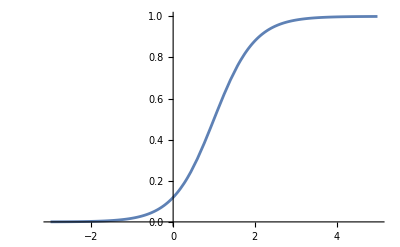

```mathematica
Plot[Sform'[t]/Sform[t]//.{H->1,Om->1,tstar->1},{t,-3,5}]
```

### Write out coefficients

```mathematica
str=strStart;

For[var=1,var<=4,var++,
field=fields[[var+1]];
For[ii=1,ii<4,ii++,
label=coeffLabels[[ii]];
str=str<>makeJuliaFunc[field,label,cosmocoeffs[[var,ii+1]]//.replfun//.replDS0];
];
label=coeffLabels[[4]];
str=str<>makeJuliaFunc[field,label,cosmocoeffs[[var,1]]//.replfun//.replDS0];
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
str
```

# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

function SCoeff0(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = (4*DS1^6*(1 - 4*LN)^2*M^2*z^8 + 4*DS0*DS1^4*(-1 + 4*LN)*M^2*z^7*(DS2*(1 - 4*LN)*z + DS1*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)) - 4*DS0^5*M*z^4*(-M + 2*M*X*z - 3*Phi*z^2 - PhiZ*z^3)*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)) + 4*DS0^6*(18 + M^2*z^2 + 4*M^2*X^2*z^4 + 2*M*PhiZ*z^5 + 9*Phi^2*z^6 + PhiZ^2*z^8 - 4*M*X*z^3*(M + PhiZ*z^3) + 6*Phi*z^4*(M - 2*M*X*z + PhiZ*z^3)) + 2*DS0^3*DS1*M*z^5*(-4*DS1^2*(-1 + 4*LN)*(-M + 2*M*X*z - 3*Phi*z^2 - PhiZ*z^3) - DS2*(-1 + 4*LN)*M*z^2*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)) + DS1*M*z*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z))) + DS0^4*M*z^4*(-4*DS1*DS2*(-1 + 4*LN)*z*(M - 2*M*X*z + 3*Phi*z^2 + PhiZ*z^3) + 4*DS1^2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)*(M - 2*M*X*z + 3*Phi*z^2 + PhiZ*z^3) + M*z^2*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z))^2) + DS0^2*DS1^2*M^2*z^6*(DS2^2*(1 - 4*LN)^2*z^2 + DS1^2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)^2 + 2*DS1*(-1 + 4*LN)*z*(2*DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z))))/(6*DS0^6)


    return co
end

function SCoeff1(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = 8*z


    return co
end

function SCoeff2(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = z^2


    return co
end

function SSrc(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = (-12*DS1^10*(1 - 4*LN)^2*LN*(-199 + 90*LN)*M^4*z^10 - 12*DS0*DS1^8*LN*(-1 + 4*LN)*M^4*z^9*(2*DS2*(-338 + 1307*LN + 180*LN^2)*z + DS1*(-499 + 1887*LN - 270*LN^2 + 3*(599 - 2486*LN + 360*LN^2)*X*z)) + 7200*DS0^10*(-M^4 + 6*M*PhiZ*z - 2*M^3*PhiZ*z^3 + 3*PhiZ^2*z^4 - M^2*PhiZ^2*z^6 + 4*M^2*X^3*z*(3 + M^2*z^2) - 4*M*X^2*z^2*(2*M^3 + PhiZ*z*(3 + M^2*z^2)) + 9*Phi^2*z^2*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) - 6*Phi*(-M + 2*M*X*z - PhiZ*z^3)*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + X*z*(5*M^4 + 6*M*PhiZ*z*(-1 + M^2*z^2) + PhiZ^2*z^4*(3 + M^2*z^2))) + DS0^2*DS1^6*LN*M^3*z^8*(9*DS2^2*(1 - 4*LN)^2*(1361 + 90*LN)*M*z^2 - 6*DS1*(-1 + 4*LN)*M*z*(-36*DS3*(-2 + 3*LN + 20*LN^2)*z + 5*DS2*(439 - 1515*LN - 270*LN^2 + 15*(-107 + 410*LN + 72*LN^2)*X*z)) + DS1^2*(54*(-733 + 5561*LN - 10606*LN^2 + 360*LN^3)*M*X*z + 4320*(1 - 4*LN)^2*p2*z^2 - 243*(1 - 4*LN)^2*(-271 + 10*LN)*M*X^2*z^2 + M*(-2430*LN^3 + 23*(339 + 80*M^2*z^2) - 4*LN*(14463 + 3680*M^2*z^2) + LN^2*(107793 + 29440*M^2*z^2)))) + DS0^3*DS1^4*M^2*z^5*(3*DS2^3*(1 - 4*LN)^2*LN*(-2453 + 180*LN)*M^2*z^5 - 6*DS1*DS2*LN*(-1 + 4*LN)*M^2*z^4*(DS3*(683 - 2462*LN - 1080*LN^2)*z + 6*DS2*(-217 + 861*LN - 135*LN^2 + 3*(272 - 1133*LN + 180*LN^2)*X*z)) + DS1^2*LN*M^2*z^3*(6*(-1 + 4*LN)*z*(250*DS4*(-1 + 4*LN)*z + DS3*(-809 + 3597*LN - 270*LN^2 + 3*(1169 - 4766*LN + 360*LN^2)*X*z)) + DS2*(-3477 - 9720*LN^3 + 18*(1339 - 9553*LN + 15708*LN^2 + 4320*LN^3)*X*z + 400*M^2*z^2 - 27*(1 - 4*LN)^2*(1519 + 360*LN)*X^2*z^2 + LN*(23022 - 3200*M^2*z^2) + LN^2*(-34533 + 6400*M^2*z^2))) + 4*DS1^3*(5400 - 43200*LN + 86400*LN^2 - 600*M^2*z^2 + 2481*LN*M^2*z^2 + 3366*LN^2*M^2*z^2 - 14985*LN^3*M^2*z^2 - 460*LN*M^4*z^4 + 3220*LN^2*M^4*z^4 - 5520*LN^3*M^4*z^4 - 1080*LN*M*p2*z^4 + 7560*LN^2*M*p2*z^4 - 12960*LN^3*M*p2*z^4 - 18*LN*(199 - 886*LN + 360*LN^2)*M*Phi*z^4 - 405*LN*(49 - 368*LN + 688*LN^2)*M^2*X^2*z^4 - 1194*LN*M*PhiZ*z^5 + 5316*LN^2*M*PhiZ*z^5 - 2160*LN^3*M*PhiZ*z^5 + 21060*(1 - 4*LN)^2*LN*M^2*X^3*z^5 + 6*LN*M*X*z^3*(540*(1 - 4*LN)^2*p2*z^2 + M*(1673 + 230*M^2*z^2 + 10*LN^2*(1737 + 368*M^2*z^2) - LN*(10997 + 1840*M^2*z^2))))) + DS0^5*DS1*M^2*z^3*(12*DS2^3*LN*(247 - 1033*LN + 180*LN^2)*M^2*z^6*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)) - 40*DS1^4*(405 - 2970*LN + 5265*LN^2 - 165*M^2*z^2 + 1440*LN*M^2*z^2 - 3015*LN^2*M^2*z^2 + 92*LN*M^4*z^4 - 368*LN^2*M^4*z^4 + 216*LN*M*p2*z^4 - 864*LN^2*M*p2*z^4 + 270*LN*M*PhiZ*z^5 - 990*LN^2*M*PhiZ*z^5 + 3888*LN*(-1 + 4*LN)*M^2*X^3*z^5 + 92*LN*M^3*PhiZ*z^7 - 368*LN^2*M^3*PhiZ*z^7 + 216*LN*p2*PhiZ*z^7 - 864*LN^2*p2*PhiZ*z^7 + 2*X*z*(-135 + 1755*LN - 4860*LN^2 + 315*M^2*z^2 - 3330*LN*M^2*z^2 + 8010*LN^2*M^2*z^2 - 92*LN*M^4*z^4 + 368*LN^2*M^4*z^4 + 216*LN*(-1 + 4*LN)*M*p2*z^4 + 45*LN*(-13 + 48*LN)*M*PhiZ*z^5) - 9*X^2*z^2*(216*LN*(-1 + 4*LN)*M*PhiZ*z^5 + 45*(7 + M^2*z^2) + 48*LN^2*(105 + 53*M^2*z^2) - 4*LN*(630 + 209*M^2*z^2)) - 6*LN*Phi*z^4*(-45*(-13 + 48*LN)*M*X*z + 108*(-1 + 4*LN)*p2*z^2 + 972*(-1 + 4*LN)*M*X^2*z^2 + M*(-135 - 46*M^2*z^2 + LN*(495 + 184*M^2*z^2)))) + DS1*DS2*LN*M*z^5*(-3*DS3^2*(1 - 4*LN)^2*(7 + 180*LN)*M*z^2 + 3*DS2*(-1 + 4*LN)*M*z*(125*DS4*(-1 + 4*LN)*z + 36*DS3*(-44 + 177*LN - 45*LN^2 + 9*(18 - 77*LN + 20*LN^2)*X*z)) + DS2^2*(54*(-547 + 4139*LN - 8164*LN^2 + 1440*LN^3)*M*X*z + 1080*(1 - 4*LN)^2*p2*z^2 - 243*(1 - 4*LN)^2*(-199 + 40*LN)*M*X^2*z^2 + M*(4953 - 9720*LN^3 + 560*M^2*z^2 - 2*LN*(17559 + 2240*M^2*z^2) + LN^2*(64917 + 8960*M^2*z^2)))) + 10*DS1^2*z^2*(3*DS3*LN*(-1 + 4*LN)*M^2*z^4*(50*DS4*(1 - 4*LN)*z + DS3*(79 - 363*LN + 363*(-1 + 4*LN)*X*z)) + 2*DS2^2*(270 - 2160*LN + 4320*LN^2 - 30*M^2*z^2 - 558*LN*M^2*z^2 + 2550*LN^2*M^2*z^2 + 729*LN^3*M^2*z^2 - 10*LN*M^4*z^4 + 70*LN^2*M^4*z^4 - 120*LN^3*M^4*z^4 + 2637*LN*(-1 + 4*LN)*M*Phi*z^4 + 243*LN*(11 - 80*LN + 144*LN^2)*M^2*X^2*z^4 - 879*LN*M*PhiZ*z^5 + 3516*LN^2*M*PhiZ*z^5 - 2916*(1 - 4*LN)^2*LN*M^2*X^3*z^5 + 6*LN*M^2*X*z^3*(158 + 5*M^2*z^2 + 2*LN^2*(-729 + 40*M^2*z^2) - LN*(281 + 40*M^2*z^2))) - 3*DS2*LN*M*z^3*(-25*DS4*(-1 + 4*LN)*M*z*(1 - 3*LN + 3*(-1 + 4*LN)*X*z) + DS3*(-6*(11 - 119*LN + 300*LN^2)*M*X*z + 72*(1 - 4*LN)^2*p2*z^2 + 153*(1 - 4*LN)^2*M*X^2*z^2 + M*(37 + 44*M^2*z^2 + 11*LN^2*(75 + 64*M^2*z^2) - 2*LN*(183 + 176*M^2*z^2))))) + DS1^3*z*(375*DS4*LN*M^2*z^4*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)^2 - 4*DS3*z*(5400 - 43200*LN + 86400*LN^2 - 600*M^2*z^2 + 4983*LN*M^2*z^2 - 8352*LN^2*M^2*z^2 - 8100*LN^3*M^2*z^2 - 230*LN*M^4*z^4 + 1610*LN^2*M^4*z^4 - 2760*LN^3*M^4*z^4 - 540*LN*M*p2*z^4 + 3780*LN^2*M*p2*z^4 - 6480*LN^3*M*p2*z^4 - 9*LN*(-271 + 994*LN + 360*LN^2)*M*Phi*z^4 - 810*LN*(15 - 112*LN + 208*LN^2)*M^2*X^2*z^4 + 813*LN*M*PhiZ*z^5 - 2982*LN^2*M*PhiZ*z^5 - 1080*LN^3*M*PhiZ*z^5 + 12960*(1 - 4*LN)^2*LN*M^2*X^3*z^5 + 6*LN*M*X*z^3*(270*(1 - 4*LN)^2*p2*z^2 + M*(479 + 115*M^2*z^2 + 20*LN^2*(495 + 92*M^2*z^2) - LN*(4361 + 920*M^2*z^2)))) + 4*DS2*(-8100 + 62100*LN - 118800*LN^2 + 2100*M^2*z^2 - 20079*LN*M^2*z^2 + 43722*LN^2*M^2*z^2 + 8505*LN^3*M^2*z^2 + 370*LN*M^4*z^4 - 2220*LN^2*M^4*z^4 + 3330*LN^3*M^4*z^4 + 810*LN*M*p2*z^4 - 4860*LN^2*M*p2*z^4 + 7290*LN^3*M*p2*z^4 - 4254*LN*M*PhiZ*z^5 + 15372*LN^2*M*PhiZ*z^5 + 2430*LN^3*M*PhiZ*z^5 - 1215*LN*(31 - 232*LN + 432*LN^2)*M^2*X^3*z^5 + 29160*(1 - 4*LN)^2*LN*M^2*X^4*z^6 - 18*LN*M*Phi*z^4*(709 - 2562*LN - 405*LN^2 + 3*(-899 + 3461*LN + 540*LN^2)*X*z) - 3*X*z*(-900 + 7200*LN - 14400*LN^2 + 900*M^2*z^2 - 13405*LN*M^2*z^2 + 31914*LN^2*M^2*z^2 + 27135*LN^3*M^2*z^2 + 740*LN*M^4*z^4 - 5180*LN^2*M^4*z^4 + 8880*LN^3*M^4*z^4 + 1620*LN*(1 - 7*LN + 12*LN^2)*M*p2*z^4 + 6*LN*(-899 + 3461*LN + 540*LN^2)*M*PhiZ*z^5) + 9*LN*M*X^2*z^4*(810*(1 - 4*LN)^2*p2*z^2 + M*(-1211 + 370*M^2*z^2 + 80*LN^2*(405 + 74*M^2*z^2) - 2*LN*(1583 + 1480*M^2*z^2)))))) + DS0^4*DS1^2*M^2*z^4*(-6*DS2^4*(1 - 4*LN)^2*LN*(-247 + 45*LN)*M^2*z^6 + 3*DS1*DS2^2*LN*(-1 + 4*LN)*M^2*z^5*(-2695*DS3*(-1 + 4*LN)*z + 2*DS2*(761 - 1983*LN - 270*LN^2 + 3*(-691 + 2674*LN + 360*LN^2)*X*z)) + 4*DS1^4*(-5400*LN + 21600*LN^2 - 1200*M^2*z^2 + 12822*LN*M^2*z^2 - 32211*LN^2*M^2*z^2 + 2835*LN^3*M^2*z^2 + 115*LN*M^4*z^4 - 690*LN^2*M^4*z^4 + 1035*LN^3*M^4*z^4 + 270*LN*M*p2*z^4 - 1620*LN^2*M*p2*z^4 + 2430*LN^3*M*p2*z^4 + 2397*LN*M*PhiZ*z^5 - 9261*LN^2*M*PhiZ*z^5 + 810*LN^3*M*PhiZ*z^5 - 405*LN*(31 - 232*LN + 432*LN^2)*M^2*X^3*z^5 + 9720*(1 - 4*LN)^2*LN*M^2*X^4*z^6 - 9*LN*M*Phi*z^4*(-799 + 3087*LN - 270*LN^2 + 27*(111 - 454*LN + 40*LN^2)*X*z) - 3*X*z*(-7200 + 57600*LN - 115200*LN^2 + 5270*LN*M^2*z^2 - 22932*LN^2*M^2*z^2 + 9045*LN^3*M^2*z^2 + 230*LN*M^4*z^4 - 1610*LN^2*M^4*z^4 + 2760*LN^3*M^4*z^4 + 540*LN*(1 - 7*LN + 12*LN^2)*M*p2*z^4 + 27*LN*(111 - 454*LN + 40*LN^2)*M*PhiZ*z^5) + 9*LN*M*X^2*z^4*(270*(1 - 4*LN)^2*p2*z^2 + M*(2793 + 115*M^2*z^2 + 80*LN^2*(135 + 23*M^2*z^2) - 2*LN*(6921 + 460*M^2*z^2)))) - DS1^2*LN*M*z^4*(9*DS3^2*(1 - 4*LN)^2*(247 + 30*LN)*M*z^2 - 6*DS2*(-1 + 4*LN)*M*z*(250*DS4*(1 - 4*LN)*z + 27*DS3*(79 - 287*LN - 30*LN^2 + 3*(-99 + 386*LN + 40*LN^2)*X*z)) + DS2^2*(-54*(797 - 5789*LN + 9864*LN^2 + 2160*LN^3)*M*X*z + 3240*(1 - 4*LN)^2*p2*z^2 + 81*(1 - 4*LN)^2*(887 + 180*LN)*M*X^2*z^2 + M*(7803 + 14580*LN^3 + 1780*M^2*z^2 - 2*LN*(27459 + 7120*M^2*z^2) + LN^2*(92367 + 28480*M^2*z^2)))) + DS1^3*z*(4*DS2*(-5400 + 43200*LN - 86400*LN^2 + 600*M^2*z^2 - 2826*LN*M^2*z^2 + 6834*LN^2*M^2*z^2 - 20655*LN^3*M^2*z^2 - 790*LN*M^4*z^4 + 5530*LN^2*M^4*z^4 - 9480*LN^3*M^4*z^4 - 1620*LN*M*p2*z^4 + 11340*LN^2*M*p2*z^4 - 19440*LN^3*M*p2*z^4 - 9*LN*(-1153 + 4342*LN + 1080*LN^2)*M*Phi*z^4 - 1215*LN*(19 - 144*LN + 272*LN^2)*M^2*X^2*z^4 + 3459*LN*M*PhiZ*z^5 - 13026*LN^2*M*PhiZ*z^5 - 3240*LN^3*M*PhiZ*z^5 + 24300*(1 - 4*LN)^2*LN*M^2*X^3*z^5 + 6*LN*M*X*z^3*(810*(1 - 4*LN)^2*p2*z^2 + M*(422 + 395*M^2*z^2 - 316*LN*(23 + 10*M^2*z^2) + 10*LN^2*(2241 + 632*M^2*z^2)))) - 5*LN*M*z^3*(-300*DS4*(-1 + 4*LN)*M*z*(1 - 3*LN + 3*(-1 + 4*LN)*X*z) + DS3*(-414*(19 - 145*LN + 276*LN^2)*M*X*z + 864*(1 - 4*LN)^2*p2*z^2 + 13419*(1 - 4*LN)^2*M*X^2*z^2 + M*(1515 + 368*M^2*z^2 - 2*LN*(5733 + 1472*M^2*z^2) + LN^2*(21483 + 5888*M^2*z^2)))))) + 2*DS0^8*M*(20*DS1^2*(-405*M - 939*M^3*z^2 + 2700*LN*M^3*z^2 - 1782*p2*z^2 + 4860*LN*p2*z^2 + 540*PhiZ*z^3 - 1620*LN*PhiZ*z^3 + 46*LN*M^5*z^4 + 108*LN*M^2*p2*z^4 - 180*M^2*PhiZ*z^5 + 720*LN*M^2*PhiZ*z^5 + 1728*LN*M^3*X^4*z^6 + 92*LN*M^4*PhiZ*z^7 + 216*LN*M*p2*PhiZ*z^7 + 90*LN*M*PhiZ^2*z^8 + 46*LN*M^3*PhiZ^2*z^10 + 108*LN*p2*PhiZ^2*z^10 + 18*LN*Phi^2*z^6*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 216*M*X^3*z^3*(8*LN*M*PhiZ*z^5 - 5*(3 + M^2*z^2) + LN*(60 + 33*M^2*z^2)) + 12*Phi*z^2*(135 - 405*LN - 45*M^2*z^2 + 180*LN*M^2*z^2 + 23*LN*M^4*z^4 + 45*LN*M*PhiZ*z^5 - 432*LN*M^2*X^3*z^5 + 23*LN*M^3*PhiZ*z^7 + 54*LN*p2*z^4*(M + PhiZ*z^3) - X*z*(270 - 1215*LN - 180*M^2*z^2 + 900*LN*M^2*z^2 + 46*LN*M^4*z^4 + 108*LN*M*p2*z^4 + 135*LN*M*PhiZ*z^5) + 27*X^2*z^2*(8*LN*M*PhiZ*z^5 - 5*(3 + M^2*z^2) + LN*(60 + 38*M^2*z^2))) - X*(270*LN*M*PhiZ^2*z^9 - 135*M*z*(11 + 8*M^2*z^2) + 2*LN*M^3*z^3*(2205 + 92*M^2*z^2) + 432*LN*M*p2*z^5*(M + PhiZ*z^3) + 4*PhiZ*z^4*(90*(3 - 2*M^2*z^2) + LN*(-1215 + 900*M^2*z^2 + 46*M^4*z^4))) + 4*X^2*z^2*(108*LN*M^2*p2*z^4 + 108*LN*M*PhiZ^2*z^8 + 27*PhiZ*z^3*(-5*(3 + M^2*z^2) + LN*(60 + 38*M^2*z^2)) + M*(-9*(183 + 55*M^2*z^2) + LN*(4050 + 2358*M^2*z^2 + 46*M^4*z^4)))) - 15*DS1*z*(-(DS3*z*(-831*M + 1350*LN*M - 80*M^3*z^2 + 414*LN*M^3*z^2 + 720*PhiZ*z^3 - 2880*LN*PhiZ*z^3 + 376*LN*M^3*X^2*z^4 - 80*M^2*PhiZ*z^5 + 508*LN*M^2*PhiZ*z^5 + 846*LN*M*Phi^2*z^6 + 94*LN*M*PhiZ^2*z^8 + 12*Phi*z^2*(180 - 720*LN - 20*M^2*z^2 + 127*LN*M^2*z^2 - 94*LN*M^2*X*z^3 + 47*LN*M*PhiZ*z^5) - 8*M*X*z*(47*LN*M*PhiZ*z^5 - 20*(-9 + M^2*z^2) + LN*(-720 + 127*M^2*z^2)))) + 4*DS2*(207*M + 80*M^3*z^2 - 342*LN*M^3*z^2 - 360*PhiZ*z^3 + 1260*LN*PhiZ*z^3 + 80*M^2*PhiZ*z^5 - 384*LN*M^2*PhiZ*z^5 + 672*LN*M^3*X^3*z^5 - 42*LN*M*PhiZ^2*z^8 + 378*LN*M*Phi^2*z^6*(-1 + 4*X*z) - 24*M*X^2*z^2*(28*LN*M*PhiZ*z^5 + 5*(6 - 2*M^2*z^2 + 3*LN*(-8 + 5*M^2*z^2))) + 12*Phi*z^2*(-90 + 315*LN + 20*M^2*z^2 - 96*LN*M^2*z^2 - 168*LN*M^2*X^2*z^4 - 21*LN*M*PhiZ*z^5 + 6*X*z*(15 - 5*M^2*z^2 + 14*LN*M*PhiZ*z^5 + LN*(-60 + 41*M^2*z^2))) + 4*X*z*(42*LN*M*PhiZ^2*z^8 + 6*PhiZ*z^3*(15 - 5*M^2*z^2 + LN*(-60 + 41*M^2*z^2)) + M*(-423 - 70*M^2*z^2 + 6*LN*(150 + 59*M^2*z^2))))) - 2*M*z^2*(15*DS3*(-1 + 4*LN)*z^2*(25*DS4*LN*M*z^3*(M - 2*M*X*z + 3*Phi*z^2 + PhiZ*z^3) + 6*DS3*(15 - 60*LN - 5*M^2*z^2 + 28*LN*M^2*z^2 + 64*LN*M^2*X^2*z^4 + 8*LN*M*PhiZ*z^5 + 24*LN*M*Phi*z^4*(1 - 4*X*z) + X*z*(-32*LN*M*PhiZ*z^5 + 5*(3 + M^2*z^2) - 4*LN*(15 + 17*M^2*z^2)))) + DS2^2*(23913 - 67500*LN + 450*M^2*z^2 - 5082*LN*M^2*z^2 + 7020*LN^2*M^2*z^2 - 560*LN*M^4*z^4 + 1680*LN^2*M^4*z^4 - 1080*LN*M*p2*z^4 + 3240*LN^2*M*p2*z^4 - 3864*LN*M*PhiZ*z^5 + 3240*LN^2*M*PhiZ*z^5 + 54*LN*(-247 + 45*LN)*Phi^2*z^6 + 25920*LN*(-1 + 4*LN)*M^2*X^4*z^6 - 560*LN*M^3*PhiZ*z^7 + 1680*LN^2*M^3*PhiZ*z^7 - 1080*LN*p2*PhiZ*z^7 + 3240*LN^2*p2*PhiZ*z^7 - 1482*LN*PhiZ^2*z^8 + 270*LN^2*PhiZ^2*z^8 + 6*X^2*z^2*(-675 + 6750*LN - 16200*LN^2 + 1125*M^2*z^2 - 13408*LN*M^2*z^2 + 30240*LN^2*M^2*z^2 - 560*LN*M^4*z^4 + 2240*LN^2*M^4*z^4 + 1080*LN*(-1 + 4*LN)*M*p2*z^4 + 90*LN*(-23 + 84*LN)*M*PhiZ*z^5) - 270*X^3*z^3*(48*LN*(-1 + 4*LN)*M*PhiZ*z^5 + 15*(3 + M^2*z^2) - 20*LN*(18 + 13*M^2*z^2) + 48*LN^2*(15 + 16*M^2*z^2)) - 2*X*z*(-3375 + 24300*LN - 42525*LN^2 + 1575*M^2*z^2 - 17364*LN*M^2*z^2 + 30915*LN^2*M^2*z^2 - 1400*LN*M^4*z^4 + 5040*LN^2*M^4*z^4 + 540*LN*p2*z^4*((-5 + 18*LN)*M + 3*(-1 + 4*LN)*PhiZ*z^3) + 6*LN*M*PhiZ*z^5*(-4*(236 + 35*M^2*z^2) + 5*LN*(333 + 112*M^2*z^2))) - 12*LN*Phi*z^4*(966*M - 810*LN*M + 140*M^3*z^2 - 420*LN*M^3*z^2 - 270*(-1 + 3*LN)*p2*z^2 - 135*(-23 + 84*LN)*M*X^2*z^2 + 741*PhiZ*z^3 - 135*LN*PhiZ*z^3 + 3240*(-1 + 4*LN)*M*X^3*z^3 + 3*X*z*(270*(-1 + 4*LN)*p2*z^2 - 4*M*(236 + 35*M^2*z^2) + 5*LN*M*(333 + 112*M^2*z^2)))) + 5*DS2*z*(-75*DS4*LN*M*z^3*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)*(M - 2*M*X*z + 3*Phi*z^2 + PhiZ*z^3) - 4*DS3*(135 - 945*LN + 1620*LN^2 - 45*M^2*z^2 + 396*LN*M^2*z^2 - 828*LN^2*M^2*z^2 + 28*LN*M^4*z^4 - 112*LN^2*M^4*z^4 + 54*LN*M*p2*z^4 - 216*LN^2*M*p2*z^4 + 81*LN*M*PhiZ*z^5 - 288*LN^2*M*PhiZ*z^5 + 1296*LN*(-1 + 4*LN)*M^2*X^3*z^5 + 28*LN*M^3*PhiZ*z^7 - 112*LN^2*M^3*PhiZ*z^7 + 54*LN*p2*PhiZ*z^7 - 216*LN^2*p2*PhiZ*z^7 + X*z*(-270 + 2295*LN - 4860*LN^2 + 180*M^2*z^2 - 1944*LN*M^2*z^2 + 4680*LN^2*M^2*z^2 - 56*LN*M^4*z^4 + 224*LN^2*M^4*z^4 + 108*LN*(-1 + 4*LN)*M*p2*z^4 + 9*LN*(-43 + 156*LN)*M*PhiZ*z^5) - 9*X^2*z^2*(72*LN*(-1 + 4*LN)*M*PhiZ*z^5 + 15*(3 + M^2*z^2) + 120*LN^2*(6 + 7*M^2*z^2) - 2*LN*(180 + 139*M^2*z^2)) - 3*LN*Phi*z^4*(-9*(-43 + 156*LN)*M*X*z + 54*(-1 + 4*LN)*p2*z^2 + 648*(-1 + 4*LN)*M*X^2*z^2 + M*(-81 - 28*M^2*z^2 + 16*LN*(18 + 7*M^2*z^2))))))) + DS0^7*M*z*(600*DS1^3*(45*M + 20*M^3*z^2 - 90*LN*M^3*z^2 - 36*PhiZ*z^3 + 180*LN*PhiZ*z^3 + 20*M^2*PhiZ*z^5 - 96*LN*M^2*PhiZ*z^5 + 96*LN*M^3*X^3*z^5 - 6*LN*M*PhiZ^2*z^8 + 54*LN*M*Phi^2*z^6*(-1 + 4*X*z) - 24*M*X^2*z^2*(-15 - M^2*z^2 + 4*LN*M*PhiZ*z^5 + LN*(60 + 9*M^2*z^2)) + 12*Phi*z^2*(-9 + 45*LN + 5*M^2*z^2 - 24*LN*M^2*z^2 - 24*LN*M^2*X^2*z^4 - 3*LN*M*PhiZ*z^5 + 3*X*z*(-15 - M^2*z^2 + 4*LN*M*PhiZ*z^5 + 10*LN*(6 + M^2*z^2))) + 4*X*z*(6*LN*M*PhiZ^2*z^8 + 3*PhiZ*z^3*(-15 - M^2*z^2 + 10*LN*(6 + M^2*z^2)) + M*(-126 - 13*M^2*z^2 + 6*LN*(60 + 11*M^2*z^2)))) + LN*M^2*z^5*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z))*(15*DS3*(-1 + 4*LN)*M*z^2*(-25*DS4*z + 48*DS3*(-1 + 4*X*z)) + 4*DS2^2*(1707*M - 945*LN*M + 140*M^3*z^2 - 420*LN*M^3*z^2 + 270*p2*z^2 - 810*LN*p2*z^2 + 18*(247 - 45*LN)*Phi*z^2 - 135*(-23 + 84*LN)*M*X^2*z^2 + 1482*PhiZ*z^3 - 270*LN*PhiZ*z^3 + 3240*(-1 + 4*LN)*M*X^3*z^3 + 3*X*z*(270*(-1 + 4*LN)*p2*z^2 - 2*M*(719 + 70*M^2*z^2) + 5*LN*M*(351 + 112*M^2*z^2))) - 5*DS2*z*(-75*DS4*M*z*(1 - 3*LN + 3*(-1 + 4*LN)*X*z) + 4*DS3*(-9*(-43 + 156*LN)*M*X*z + 54*(-1 + 4*LN)*p2*z^2 + 648*(-1 + 4*LN)*M*X^2*z^2 + M*(-81 - 28*M^2*z^2 + 16*LN*(18 + 7*M^2*z^2))))) + 20*DS1*M*z^2*(-3*DS3^2*(-1 + 4*LN)*z^2*(90 - 360*LN - 10*M^2*z^2 + 87*LN*M^2*z^2 - 94*LN*M^2*X*z^3 + 141*LN*M*Phi*z^4 + 47*LN*M*PhiZ*z^5) + 2*DS2^2*(405 - 2700*LN + 4455*LN^2 - 105*M^2*z^2 + 936*LN*M^2*z^2 - 1953*LN^2*M^2*z^2 + 56*LN*M^4*z^4 - 224*LN^2*M^4*z^4 + 108*LN*M*p2*z^4 - 432*LN^2*M*p2*z^4 + 216*LN*M*PhiZ*z^5 - 738*LN^2*M*PhiZ*z^5 + 3888*LN*(-1 + 4*LN)*M^2*X^3*z^5 + 56*LN*M^3*PhiZ*z^7 - 224*LN^2*M^3*PhiZ*z^7 + 108*LN*p2*PhiZ*z^7 - 432*LN^2*p2*PhiZ*z^7 + 2*X*z*(-675 + 5130*LN - 9720*LN^2 + 225*M^2*z^2 - 2502*LN*M^2*z^2 + 6030*LN^2*M^2*z^2 - 56*LN*M^4*z^4 + 224*LN^2*M^4*z^4 + 108*LN*(-1 + 4*LN)*M*p2*z^4 + 36*LN*(-16 + 57*LN)*M*PhiZ*z^5) - 9*X^2*z^2*(216*LN*(-1 + 4*LN)*M*PhiZ*z^5 + LN*(360 - 832*M^2*z^2) + 45*(-1 + M^2*z^2) + 48*LN^2*(-15 + 52*M^2*z^2)) - 6*LN*Phi*z^4*(-36*(-16 + 57*LN)*M*X*z + 54*(-1 + 4*LN)*p2*z^2 + 972*(-1 + 4*LN)*M*X^2*z^2 - 4*M*(27 + 7*M^2*z^2) + LN*M*(369 + 112*M^2*z^2))) + 3*DS2*z*(25*DS4*LN*(-1 + 4*LN)*M*z^3*(-M + 2*M*X*z - 3*Phi*z^2 - PhiZ*z^3) + DS3*(360 - 2700*LN + 5040*LN^2 - 80*M^2*z^2 + 799*LN*M^2*z^2 - 1869*LN^2*M^2*z^2 - 1338*LN*(-1 + 4*LN)*M^2*X^2*z^4 + 179*LN*M*PhiZ*z^5 - 669*LN^2*M*PhiZ*z^5 + 3*LN*M*Phi*z^4*(179 - 669*LN + 669*(-1 + 4*LN)*X*z) + X*z*(669*LN*(-1 + 4*LN)*M*PhiZ*z^5 + LN*(2880 - 1987*M^2*z^2) + 120*(-3 + M^2*z^2) + 6*LN^2*(-960 + 989*M^2*z^2))))) - 2*DS1^2*z*(-10*M*z*(75*DS4*LN*M*z^3*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)*(M - 2*M*X*z + 3*Phi*z^2 + PhiZ*z^3) + 4*DS3*(135 - 945*LN + 1620*LN^2 - 45*M^2*z^2 + 396*LN*M^2*z^2 - 828*LN^2*M^2*z^2 + 23*LN*M^4*z^4 - 92*LN^2*M^4*z^4 + 54*LN*M*p2*z^4 - 216*LN^2*M*p2*z^4 + 81*LN*M*PhiZ*z^5 - 288*LN^2*M*PhiZ*z^5 + 1296*LN*(-1 + 4*LN)*M^2*X^3*z^5 + 23*LN*M^3*PhiZ*z^7 - 92*LN^2*M^3*PhiZ*z^7 + 54*LN*p2*PhiZ*z^7 - 216*LN^2*p2*PhiZ*z^7 + X*z*(-270 + 2295*LN - 4860*LN^2 + 180*M^2*z^2 - 1944*LN*M^2*z^2 + 4680*LN^2*M^2*z^2 - 46*LN*M^4*z^4 + 184*LN^2*M^4*z^4 + 108*LN*(-1 + 4*LN)*M*p2*z^4 + 9*LN*(-43 + 156*LN)*M*PhiZ*z^5) - 9*X^2*z^2*(72*LN*(-1 + 4*LN)*M*PhiZ*z^5 + 15*(3 + M^2*z^2) + 120*LN^2*(6 + 7*M^2*z^2) - 2*LN*(180 + 139*M^2*z^2)) - 3*LN*Phi*z^4*(-9*(-43 + 156*LN)*M*X*z + 54*(-1 + 4*LN)*p2*z^2 + 648*(-1 + 4*LN)*M*X^2*z^2 + M*(-81 - 23*M^2*z^2 + 4*LN*(72 + 23*M^2*z^2))))) + 3*DS2*(-20061*M + 56250*LN*M + 1000*M^3*z^2 - 5446*LN*M^3*z^2 + 9360*LN^2*M^3*z^2 - 3600*PhiZ*z^3 + 14400*LN*PhiZ*z^3 - 680*LN*M^5*z^4 + 2040*LN^2*M^5*z^4 - 1440*LN*M^2*p2*z^4 + 4320*LN^2*M^2*p2*z^4 + 400*M^2*PhiZ*z^5 - 892*LN*M^2*PhiZ*z^5 + 4320*LN^2*M^2*PhiZ*z^5 + 162*LN*(53 + 20*LN)*M*Phi^2*z^6 + 34560*LN*(-1 + 4*LN)*M^3*X^4*z^6 - 680*LN*M^4*PhiZ*z^7 + 2040*LN^2*M^4*PhiZ*z^7 - 1440*LN*M*p2*PhiZ*z^7 + 4320*LN^2*M*p2*PhiZ*z^7 + 954*LN*M*PhiZ^2*z^8 + 360*LN^2*M*PhiZ^2*z^8 + 24*M*X^2*z^2*(-225 + 2250*LN - 5400*LN^2 + 375*M^2*z^2 - 3981*LN*M^2*z^2 + 10080*LN^2*M^2*z^2 - 170*LN*M^4*z^4 + 680*LN^2*M^4*z^4 + 360*LN*(-1 + 4*LN)*M*p2*z^4 + 30*LN*(-23 + 84*LN)*M*PhiZ*z^5) - 360*M*X^3*z^3*(48*LN*(-1 + 4*LN)*M*PhiZ*z^5 + 15*(3 + M^2*z^2) - 20*LN*(18 + 13*M^2*z^2) + 48*LN^2*(15 + 16*M^2*z^2)) - 8*M*X*z*(-2025 + 11700*LN - 14175*LN^2 + 625*M^2*z^2 - 4723*LN*M^2*z^2 + 10305*LN^2*M^2*z^2 - 425*LN*M^4*z^4 + 1530*LN^2*M^4*z^4 + 180*LN*p2*z^4*((-5 + 18*LN)*M + 3*(-1 + 4*LN)*PhiZ*z^3) + 3*LN*M*PhiZ*z^5*(-141 - 85*M^2*z^2 + 10*LN*(111 + 34*M^2*z^2))) - 12*Phi*z^2*(900 - 3600*LN - 100*M^2*z^2 + 223*LN*M^2*z^2 - 1080*LN^2*M^2*z^2 + 170*LN*M^4*z^4 - 510*LN^2*M^4*z^4 - 360*LN*(-1 + 3*LN)*M*p2*z^4 - 180*LN*(-23 + 84*LN)*M^2*X^2*z^4 - 477*LN*M*PhiZ*z^5 - 180*LN^2*M*PhiZ*z^5 + 4320*LN*(-1 + 4*LN)*M^2*X^3*z^5 + 6*LN*M*X*z^3*(180*(-1 + 4*LN)*p2*z^2 + M*(-141 - 85*M^2*z^2 + 10*LN*(111 + 34*M^2*z^2))))))) + 10*DS0^9*(-240*DS1*(4*M^2*X^2*z*(-9 + M^2*z^2) + 9*Phi^2*z^3*(-9 + M^2*z^2) - 4*M*X*(-9 + M^2*z^2)*(M + PhiZ*z^3) + 6*Phi*z*(-9 + M^2*z^2)*(M - 2*M*X*z + PhiZ*z^3) + z*(M^4 + 2*M*PhiZ*z*(-9 + M^2*z^2) + PhiZ^2*z^4*(-9 + M^2*z^2))) + M*(4*DS2*(-405*M - 1104*M^3*z^2 + 3150*LN*M^3*z^2 - 1782*p2*z^2 + 4860*LN*p2*z^2 + 540*PhiZ*z^3 - 1620*LN*PhiZ*z^3 + 56*LN*M^5*z^4 + 108*LN*M^2*p2*z^4 - 180*M^2*PhiZ*z^5 + 720*LN*M^2*PhiZ*z^5 + 1728*LN*M^3*X^4*z^6 + 112*LN*M^4*PhiZ*z^7 + 216*LN*M*p2*PhiZ*z^7 + 90*LN*M*PhiZ^2*z^8 + 56*LN*M^3*PhiZ^2*z^10 + 108*LN*p2*PhiZ^2*z^10 + 18*LN*Phi^2*z^6*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 216*M*X^3*z^3*(8*LN*M*PhiZ*z^5 - 5*(3 + M^2*z^2) + LN*(60 + 33*M^2*z^2)) + 12*Phi*z^2*(135 - 405*LN - 45*M^2*z^2 + 180*LN*M^2*z^2 + 28*LN*M^4*z^4 + 45*LN*M*PhiZ*z^5 - 432*LN*M^2*X^3*z^5 + 28*LN*M^3*PhiZ*z^7 + 54*LN*p2*z^4*(M + PhiZ*z^3) - X*z*(270 - 1215*LN - 180*M^2*z^2 + 900*LN*M^2*z^2 + 56*LN*M^4*z^4 + 108*LN*M*p2*z^4 + 135*LN*M*PhiZ*z^5) + 27*X^2*z^2*(8*LN*M*PhiZ*z^5 - 5*(3 + M^2*z^2) + LN*(60 + 38*M^2*z^2))) - X*(270*LN*M*PhiZ^2*z^9 - 135*M*z*(11 + 8*M^2*z^2) + 14*LN*M^3*z^3*(315 + 16*M^2*z^2) + 432*LN*M*p2*z^5*(M + PhiZ*z^3) + 4*PhiZ*z^4*(90*(3 - 2*M^2*z^2) + LN*(-1215 + 900*M^2*z^2 + 56*M^4*z^4))) + 4*X^2*z^2*(108*LN*M^2*p2*z^4 + 108*LN*M*PhiZ^2*z^8 + 27*PhiZ*z^3*(-5*(3 + M^2*z^2) + LN*(60 + 38*M^2*z^2)) + M*(-9*(183 + 55*M^2*z^2) + LN*(4050 + 2358*M^2*z^2 + 56*M^4*z^4)))) - 3*z*(-25*DS4*M*z*(-33 + 90*LN + 2*LN*M^2*z^2 + 8*LN*M^2*X^2*z^4 + 4*LN*M*PhiZ*z^5 + 18*LN*Phi^2*z^6 + 2*LN*PhiZ^2*z^8 - 8*LN*M*X*z^3*(M + PhiZ*z^3) + 12*LN*Phi*z^4*(M - 2*M*X*z + PhiZ*z^3)) + 48*DS3*(12*M + 5*M^3*z^2 - 22*LN*M^3*z^2 - 15*PhiZ*z^3 + 60*LN*PhiZ*z^3 + 5*M^2*PhiZ*z^5 - 24*LN*M^2*PhiZ*z^5 + 32*LN*M^3*X^3*z^5 - 2*LN*M*PhiZ^2*z^8 + 18*LN*M*Phi^2*z^6*(-1 + 4*X*z) - 2*M*X^2*z^2*(-15 - 5*M^2*z^2 + 16*LN*M*PhiZ*z^5 + 20*LN*(3 + 2*M^2*z^2)) + X*z*(8*LN*M*PhiZ^2*z^8 + M*(-3*(39 + 5*M^2*z^2) + 4*LN*(75 + 19*M^2*z^2)) + PhiZ*z^3*(-5*(3 + M^2*z^2) + LN*(60 + 44*M^2*z^2))) + 3*Phi*z^2*(-15 + 60*LN + 5*M^2*z^2 - 24*LN*M^2*z^2 - 32*LN*M^2*X^2*z^4 - 4*LN*M*PhiZ*z^5 + X*z*(16*LN*M*PhiZ*z^5 - 5*(3 + M^2*z^2) + LN*(60 + 44*M^2*z^2))))))) + DS0^6*M*z^2*(-6*DS2^2*LN*(-247 + 45*LN)*M^3*z^6*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z))^2 - 60*DS1^3*M*z*(50*DS4*LN*(-1 + 4*LN)*M*z^4*(-M + 2*M*X*z - 3*Phi*z^2 - PhiZ*z^3) + DS3*z*(180 - 1620*LN + 3600*LN^2 - 100*M^2*z^2 + 929*LN*M^2*z^2 - 2163*LN^2*M^2*z^2 - 966*LN*(-1 + 4*LN)*M^2*X^2*z^4 + 109*LN*M*PhiZ*z^5 - 483*LN^2*M*PhiZ*z^5 + 3*LN*M*Phi*z^4*(109 - 483*LN + 483*(-1 + 4*LN)*X*z) + X*z*(483*LN*(-1 + 4*LN)*M*PhiZ*z^5 + 60*(15 + M^2*z^2) + 6*LN^2*(2400 + 643*M^2*z^2) - LN*(7200 + 1181*M^2*z^2))) + 4*DS2*(-45*LN + 135*LN^2 - 10*M^2*z^2 + 84*LN*M^2*z^2 - 177*LN^2*M^2*z^2 + 11*LN*M^4*z^4 - 44*LN^2*M^4*z^4 + 18*LN*M*p2*z^4 - 72*LN^2*M*p2*z^4 + 9*LN*M*PhiZ*z^5 - 42*LN^2*M*PhiZ*z^5 + 11*LN*M^3*PhiZ*z^7 - 44*LN^2*M^3*PhiZ*z^7 + 18*LN*p2*PhiZ*z^7 - 72*LN^2*p2*PhiZ*z^7 + X*z*(180 - 1125*LN + 1620*LN^2 + 30*M^2*z^2 - 276*LN*M^2*z^2 + 660*LN^2*M^2*z^2 - 22*LN*M^4*z^4 + 88*LN^2*M^4*z^4 + 36*LN*(-1 + 4*LN)*M*p2*z^4 + 3*LN*(-1 + 12*LN)*M*PhiZ*z^5) - 6*X^2*z^2*(90 + 12*LN^2*(120 + M^2*z^2) - LN*(720 + M^2*z^2)) - 3*LN*Phi*z^4*(3*(1 - 12*LN)*M*X*z + 18*(-1 + 4*LN)*p2*z^2 + M*(-9 - 11*M^2*z^2 + LN*(42 + 44*M^2*z^2))))) - 2*DS1^4*(40221*M - 141750*LN*M - 1500*M^3*z^2 + 1206*LN*M^3*z^2 + 14040*LN^2*M^3*z^2 + 21600*PhiZ*z^3 - 86400*LN*PhiZ*z^3 - 920*LN*M^5*z^4 + 2760*LN^2*M^5*z^4 - 2160*LN*M^2*p2*z^4 + 6480*LN^2*M^2*p2*z^4 - 2400*M^2*PhiZ*z^5 + 5412*LN*M^2*PhiZ*z^5 + 6480*LN^2*M^2*PhiZ*z^5 + 54*LN*(-199 + 90*LN)*M*Phi^2*z^6 + 51840*LN*(-1 + 4*LN)*M^3*X^4*z^6 - 920*LN*M^4*PhiZ*z^7 + 2760*LN^2*M^4*PhiZ*z^7 - 2160*LN*M*p2*PhiZ*z^7 + 6480*LN^2*M*p2*PhiZ*z^7 - 1194*LN*M*PhiZ^2*z^8 + 540*LN^2*M*PhiZ^2*z^8 + 12*M*X^2*z^2*(-675 + 6750*LN - 16200*LN^2 + 1125*M^2*z^2 - 12818*LN*M^2*z^2 + 30240*LN^2*M^2*z^2 - 460*LN*M^4*z^4 + 1840*LN^2*M^4*z^4 + 1080*LN*(-1 + 4*LN)*M*p2*z^4 + 90*LN*(-23 + 84*LN)*M*PhiZ*z^5) - 540*M*X^3*z^3*(48*LN*(-1 + 4*LN)*M*PhiZ*z^5 + 15*(3 + M^2*z^2) - 20*LN*(18 + 13*M^2*z^2) + 48*LN^2*(15 + 16*M^2*z^2)) - 4*M*X*z*(7425 - 18900*LN - 42525*LN^2 + 375*M^2*z^2 - 10794*LN*M^2*z^2 + 30915*LN^2*M^2*z^2 - 1150*LN*M^4*z^4 + 4140*LN^2*M^4*z^4 + 540*LN*p2*z^4*((-5 + 18*LN)*M + 3*(-1 + 4*LN)*PhiZ*z^3) + 6*LN*M*PhiZ*z^5*(-649 - 115*M^2*z^2 + 5*LN*(333 + 92*M^2*z^2))) - 12*Phi*z^2*(-5400 + 21600*LN + 600*M^2*z^2 - 1353*LN*M^2*z^2 - 1620*LN^2*M^2*z^2 + 230*LN*M^4*z^4 - 690*LN^2*M^4*z^4 - 540*LN*(-1 + 3*LN)*M*p2*z^4 - 270*LN*(-23 + 84*LN)*M^2*X^2*z^4 + 597*LN*M*PhiZ*z^5 - 270*LN^2*M*PhiZ*z^5 + 6480*LN*(-1 + 4*LN)*M^2*X^3*z^5 + 6*LN*M*X*z^3*(270*(-1 + 4*LN)*p2*z^2 + M*(-649 - 115*M^2*z^2 + 5*LN*(333 + 92*M^2*z^2))))) + DS1*LN*M^2*z^5*(705*DS3^3*(1 - 4*LN)^2*M*z^3 - 30*DS2*DS3*(-1 + 4*LN)*M*z^2*(25*DS4*(1 - 4*LN)*z + DS3*(137 - 501*LN + 501*(-1 + 4*LN)*X*z)) - 4*DS2^3*(-2247*M + 11238*LN*M - 9315*LN^2*M - 280*M^3*z^2 + 1960*LN*M^3*z^2 - 3360*LN^2*M^3*z^2 - 540*p2*z^2 + 3780*LN*p2*z^2 - 6480*LN^2*p2*z^2 - 18*(247 - 1033*LN + 180*LN^2)*Phi*z^2 - 405*(41 - 304*LN + 560*LN^2)*M*X^2*z^2 - 1482*PhiZ*z^3 + 6198*LN*PhiZ*z^3 - 1080*LN^2*PhiZ*z^3 + 17820*(1 - 4*LN)^2*M*X^3*z^3 + 6*X*z*(270*(1 - 4*LN)^2*p2*z^2 + M*(1469 + 140*M^2*z^2 + 10*LN^2*(1233 + 224*M^2*z^2) - 2*LN*(4453 + 560*M^2*z^2)))) + 5*DS2^2*z*(-150*DS4*(-1 + 4*LN)*M*z*(1 - 3*LN + 3*(-1 + 4*LN)*X*z) + DS3*(-18*(415 - 3097*LN + 5748*LN^2)*M*X*z + 432*(1 - 4*LN)^2*p2*z^2 + 12501*(1 - 4*LN)^2*M*X^2*z^2 + M*(1293 + 224*M^2*z^2 - 2*LN*(4635 + 896*M^2*z^2) + LN^2*(16533 + 3584*M^2*z^2))))) + 2*DS1^2*M*z^2*(5*DS3*LN*(-1 + 4*LN)*M*z^4*(-75*DS4*M*z*(1 - 3*LN + 3*(-1 + 4*LN)*X*z) + 2*DS3*(-9*(-71 + 252*LN)*M*X*z + 54*(-1 + 4*LN)*p2*z^2 + 1080*(-1 + 4*LN)*M*X^2*z^2 + M*(-117 - 23*M^2*z^2 + 4*LN*(99 + 23*M^2*z^2)))) + 2*DS2^2*(4050 - 29700*LN + 54000*LN^2 - 750*M^2*z^2 + 7686*LN*M^2*z^2 - 20853*LN^2*M^2*z^2 + 8505*LN^3*M^2*z^2 + 395*LN*M^4*z^4 - 2370*LN^2*M^4*z^4 + 3555*LN^3*M^4*z^4 + 810*LN*M*p2*z^4 - 4860*LN^2*M*p2*z^4 + 7290*LN^3*M*p2*z^4 + 1311*LN*M*PhiZ*z^5 - 6003*LN^2*M*PhiZ*z^5 + 2430*LN^3*M*PhiZ*z^5 - 1215*LN*(31 - 232*LN + 432*LN^2)*M^2*X^3*z^5 + 29160*(1 - 4*LN)^2*LN*M^2*X^4*z^6 - 9*LN*M*Phi*z^4*(-437 + 2001*LN - 810*LN^2 + 3*(577 - 2578*LN + 1080*LN^2)*X*z) - 3*X*z*(2250 - 18000*LN + 36000*LN^2 - 450*M^2*z^2 + 8230*LN*M^2*z^2 - 32436*LN^2*M^2*z^2 + 27135*LN^3*M^2*z^2 + 790*LN*M^4*z^4 - 5530*LN^2*M^4*z^4 + 9480*LN^3*M^4*z^4 + 1620*LN*(1 - 7*LN + 12*LN^2)*M*p2*z^4 + 3*LN*(577 - 2578*LN + 1080*LN^2)*M*PhiZ*z^5) + 9*LN*M*X^2*z^4*(810*(1 - 4*LN)^2*p2*z^2 + M*(3539 + 395*M^2*z^2 + 80*LN^2*(405 + 79*M^2*z^2) - 2*LN*(11083 + 1580*M^2*z^2)))) - 3*DS2*z*(-125*DS4*LN*M^2*z^3*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)^2 + 4*DS3*(-450 + 3600*LN - 7200*LN^2 + 50*M^2*z^2 - 489*LN*M^2*z^2 + 1816*LN^2*M^2*z^2 - 2700*LN^3*M^2*z^2 - 85*LN*M^4*z^4 + 595*LN^2*M^4*z^4 - 1020*LN^3*M^4*z^4 - 180*LN*M*p2*z^4 + 1260*LN^2*M*p2*z^4 - 2160*LN^3*M*p2*z^4 - 3*LN*(-121 + 394*LN + 360*LN^2)*M*Phi*z^4 - 270*LN*(15 - 112*LN + 208*LN^2)*M^2*X^2*z^4 + 121*LN*M*PhiZ*z^5 - 394*LN^2*M*PhiZ*z^5 - 360*LN^3*M*PhiZ*z^5 + 4320*(1 - 4*LN)^2*LN*M^2*X^3*z^5 + LN*M*X*z^3*(540*(1 - 4*LN)^2*p2*z^2 + M*(17*(74 + 15*M^2*z^2) + 120*LN^2*(165 + 34*M^2*z^2) - 2*LN*(4961 + 1020*M^2*z^2))))))))/(32400*DS0^9)


    return co
end

function SdotCoeff0(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = (2*z^5*(-3*DS1^4*(199 - 1374*LN + 540*LN^2)*M^2*z^5 + 9*DS0*DS1^2*M^2*z^4*(-3*DS2*(-53 + 278*LN + 120*LN^2)*z + 100*DS1*(1 - 5*LN + 4*(-1 + 6*LN)*X*z)) + 1800*DS0^4*(-2*M^2*z + 3*X*(1 + M^2*z^2)) + DS0^2*M*z^3*(-6*DS2^2*(247 - 1572*LN + 270*LN^2)*M*z^2 - 15*DS1*M*z*(47*DS3*(1 - 6*LN)*z + 84*DS2*(1 - 5*LN + 4*(-1 + 6*LN)*X*z)) + 20*DS1^2*(-135*(-1 + 5*LN)*M*X*z + 54*(-1 + 6*LN)*p2*z^2 + 216*(-1 + 6*LN)*M*X^2*z^2 + M*(-45 - 23*M^2*z^2 + 6*LN*(30 + 23*M^2*z^2)))) + 5*DS0^3*(4320*S*z^3 - 360*DS1*(-3 + M^2*z^2) + z^3*(1080*SZ*z + M*(3*M*z*(25*DS4*(-1 + 6*LN)*z - 48*DS3*(1 - 5*LN + 4*(-1 + 6*LN)*X*z)) + 4*DS2*(-135*(-1 + 5*LN)*M*X*z + 54*(-1 + 6*LN)*p2*z^2 + 216*(-1 + 6*LN)*M*X^2*z^2 + M*(-45 - 28*M^2*z^2 + 12*LN*(15 + 14*M^2*z^2))))))))/(3*DS1^4*(199 - 90*LN)*LN*M^2*z^6 - 9*DS0*DS1^2*LN*M^2*z^5*(3*DS2*(53 + 20*LN)*z - 100*DS1*(-1 + 4*X*z)) + 1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + DS0^2*LN*M*z^4*(6*DS2^2*(247 - 45*LN)*M*z^2 + 20*DS1^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 15*DS1*M*z*(-47*DS3*z + 84*DS2*(-1 + 4*X*z))) + 5*DS0^3*(1080*S*z^4 - 120*DS1*z*(-9 + M^2*z^2) + LN*M*z^4*(4*DS2*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 3*M*z*(25*DS4*z - 48*DS3*(-1 + 4*X*z)))))


    return co
end

function SdotCoeff1(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = z^5


    return co
end

function SdotCoeff2(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = 0


    return co
end

function SdotSrc(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = -1/8100*(9*DS1^8*(199 - 90*LN)^2*LN^2*M^4*V*z^12 + 54*DS0*DS1^6*LN*M^4*z^11*(3*DS2*LN*(-10547 + 790*LN + 1800*LN^2)*V*z - 25*DS1*(-1791 + 9111*LN - 3510*LN^2 + 4*LN*(-199 + 90*LN)*V*(-1 + 4*X*z))) + 1620000*DS0^8*(54 - 9*M^2*z^2 - 3*M^4*z^4 - 18*M^2*X^3*z^5 - 18*X^2*z^2*(-3 + M^2*z^2) + 6*X*z*(18 + M^4*z^4) + 2*V*(3 - M^2*z^2 + X*z*(3 + M^2*z^2))^2) - 3*DS0^2*DS1^4*M^2*z^8*(-3*DS2^2*LN^2*(424141 + 46980*LN + 48600*LN^2)*M^2*V*z^4 + 30*DS1*LN*M^2*z^3*(47*DS3*LN*(-199 + 90*LN)*V*z + 6*DS2*(-27*(-696 + 2991*LN + 65*LN^2) + 4*LN*(1889 + 135*LN)*V*(-1 + 4*X*z))) + 5*DS1^2*(-405*(796 - 1080*LN^3*M^2*z^2 + 2*LN*(1797 - 8237*LN + 1170*LN^2)*M^2*X*z^3 - LN*(4700 + 1197*M^2*z^2) + 2*LN^2*(900 + 2519*M^2*z^2)) + 8*LN^2*M*V*z^2*(-135*(-599 + 90*LN)*M*X*z + 54*(-199 + 90*LN)*p2*z^2 + 648*(-233 + 30*LN)*M*X^2*z^2 + M*(-15705 - 4577*M^2*z^2 + 90*LN*(45 + 23*M^2*z^2))))) - 6*DS0^3*DS1^2*M^2*z^7*(5400*DS1^2*LN*(-199 + 90*LN)*S*V*z^3 + 54*DS2^3*LN^2*(13091 + 2555*LN - 900*LN^2)*M^2*V*z^5 - 45*DS1*DS2*LN*M^2*z^4*(-141*DS3*LN*(53 + 20*LN)*V*z + DS2*(60867 - 246207*LN - 45630*LN^2 + 4*LN*(5809 + 810*LN)*V*(-1 + 4*X*z))) - 150*DS1^3*(4*LN*V*(1791 - 810*LN - 199*M^2*z^2 - 360*LN*M^2*z^2 - 230*LN*M^4*z^4 - 540*LN*M*p2*z^4 - 7560*LN*M^2*X^2*z^4 + 8640*LN*M^2*X^3*z^5 + 10*LN*M*X*z^3*(315*M + 92*M^3*z^2 + 216*p2*z^2)) - 3*(-882 + 8559*LN - 7290*LN^2 + 796*M^2*z^2 - 8473*LN*M^2*z^2 + 12780*LN^2*M^2*z^2 - 690*LN*M^4*z^4 + 2990*LN^2*M^4*z^4 + 540*LN*(-3 + 13*LN)*M*p2*z^4 + 7560*LN*(-3 + 13*LN)*M^2*X^2*z^4 - 18*X*z*(799 + 150*LN^2*(3 + 23*M^2*z^2) - 25*LN*(167 + 36*M^2*z^2)))) + 5*DS1^2*z*(-3*LN*M^2*z^3*(25*DS4*(199 - 90*LN)*LN*V*z + 3*DS3*(14157 - 64047*LN + 7020*LN^2 + 4*LN*(379 + 360*LN)*V*(-1 + 4*X*z))) + DS2*(-1350*LN*(-1641 + 6886*LN + 585*LN^2)*M^2*X*z^3 + 405*(954 + 900*LN^3*M^2*z^2 - 25*LN*(162 + 71*M^2*z^2) + 15*LN^2*(-120 + 427*M^2*z^2)) + 4*LN^2*M*V*z^2*(-810*(233 + 45*LN)*M*X*z + 108*(139 + 135*LN)*p2*z^2 + 432*(839 + 135*LN)*M*X^2*z^2 + M*(31410 + 5399*M^2*z^2 + 90*LN*(135 + 74*M^2*z^2)))))) + DS0^4*M*z^6*(36*DS2^4*(247 - 45*LN)^2*LN^2*M^3*V*z^6 + 97200*DS1^2*M*S*z^3*(-3*DS2*LN*(53 + 20*LN)*V*z + 25*DS1*(3 - 27*LN + 4*LN*V*(-1 + 4*X*z))) + 180*DS1*DS2^2*LN*M^3*z^5*(47*DS3*(247 - 45*LN)*LN*V*z + 3*DS2*(-27*(741 - 3436*LN + 585*LN^2) + 28*LN*(-247 + 45*LN)*V*(-1 + 4*X*z))) - 75*DS1^3*M*z*(-76140*DS3*z + 380700*DS3*LN*z + 37665*DS3*LN*M^2*z^3 - 157140*DS3*LN^2*M^2*z^3 + 194400*LN*SZ*z^3 + 360*DS3*LN^2*M^2*V*z^3 - 20250*DS4*LN*M^2*z^4 + 87750*DS4*LN^2*M^2*z^4 + 9000*DS4*LN^2*M^2*V*z^4 - 36450*DS3*LN*M^2*X*z^4 + 157950*DS3*LN^2*M^2*X*z^4 - 87480*DS3*LN^2*M^2*V*X*z^4 - 8648*DS3*LN^2*M^4*V*z^5 - 20304*DS3*LN^2*M*p2*V*z^5 - 36000*DS4*LN^2*M^2*V*X*z^5 + 195264*DS3*LN^2*M^2*V*X^2*z^5 + 36*DS2*(4806 - 17037*LN - 14580*LN^2 + 23706*X*z - 112050*LN*X*z - 16200*LN^2*X*z - 1908*M^2*z^2 + 13644*LN*M^2*z^2 - 10980*LN^2*M^2*z^2 - 24300*LN*M^2*X*z^3 + 93780*LN^2*M^2*X*z^3 + 402*LN*M^4*z^4 - 1742*LN^2*M^4*z^4 + 1296*LN*M*p2*z^4 - 5616*LN^2*M*p2*z^4 + 33264*LN*M^2*X^2*z^4 - 144144*LN^2*M^2*X^2*z^4 + 4*LN*V*(1431 + 540*LN - 159*M^2*z^2 - 120*LN*M^2*z^2 - 14*LN*M^4*z^4 - 72*LN*M*p2*z^4 - 1008*LN*M^2*X^2*z^4 + 1152*LN*M^2*X^3*z^5 + 4*LN*M*X*z^3*(105*M + 14*M^3*z^2 + 72*p2*z^2)))) + 100*DS1^4*(4*LN*M*V*(-8181 - 7290*LN - 2673*M^2*z^2 + 4455*LN*M^2*z^2 + 2070*LN*M^4*z^4 + 4860*LN*M*p2*z^4 - 58320*LN*M^2*X^3*z^5 + 529*LN*M^6*z^6 + 2484*LN*M^3*p2*z^6 + 2916*LN*p2^2*z^6 + 46656*LN*M^2*X^4*z^6 + 27*LN*M*X^2*z^4*(1395*M + 368*M^3*z^2 + 864*p2*z^2) - 27*X*z*(-4197 + 201*M^2*z^2 + 540*LN*M*p2*z^4 + 10*LN*(27 + 54*M^2*z^2 + 23*M^4*z^4))) - 81*(2160*LN*(-3 + 13*LN)*M^3*X^3*z^5 - 270*p2*z^2*(4 + 12*LN^2*M^2*z^2 - LN*(20 + 3*M^2*z^2)) - 3*M*X^2*z^2*(4039 + 90*LN^2*(5 + 103*M^2*z^2) - 5*LN*(4075 + 486*M^2*z^2)) + M*X*z*(-3894 + 1600*M^2*z^2 + 540*LN*(-3 + 13*LN)*M*p2*z^4 + LN*(20853 - 12175*M^2*z^2 - 690*M^4*z^4) + 10*LN^2*(-243 + 1080*M^2*z^2 + 299*M^4*z^4)) - M*(597 + 561*M^2*z^2 + 30*LN^2*(36 + 45*M^2*z^2 + 46*M^4*z^4) - LN*(2028 + 2900*M^2*z^2 + 345*M^4*z^4)))) - 15*DS1^2*M*z^2*(-33135*DS3^2*LN^2*M^2*V*z^4 - 18*DS2*LN*M^2*z^3*(-75*DS4*LN*(53 + 20*LN)*V*z + DS3*(27*(-1023 + 4233*LN + 520*LN^2) + 4*LN*(263 + 720*LN)*V*(-1 + 4*X*z))) + DS2^2*(-405*(1976 - 360*LN^3*M^2*z^2 + 2*LN*(4983 - 21743*LN + 390*LN^2)*M^2*X*z^3 + 30*LN^2*(60 + 451*M^2*z^2) - LN*(10600 + 3471*M^2*z^2)) + 8*LN^2*M*V*z^2*(-1215*(-89 + 30*LN)*M*X*z + 54*(-17 + 270*LN)*p2*z^2 + 216*(-997 + 270*LN)*M*X^2*z^2 + M*(-13995 + 1994*M^2*z^2 + 90*LN*(135 + 79*M^2*z^2)))))) + 25*DS0^6*z^2*(1166400*S^2*V*z^6 + 1080*S*(-60*DS1*z^3*(135 + 162*X*z - 42*M^2*z^2 + 4*V*(-9 + M^2*z^2)) + M*z^6*(DS2*(135*M*(1 - 8*LN + 2*(-1 + 9*LN)*X*z) + 8*LN*V*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2)) + 6*M*z*(25*DS4*LN*V*z - 6*DS3*(-3 + 27*LN + 8*LN*V*(-1 + 4*X*z))))) + 360*DS1^2*(8*V*(405 - 90*M^2*z^2 + 135*LN*M^2*z^2 + 5*M^4*z^4 + 24*LN*M^4*z^4 - 23*LN*M^6*z^6 - 54*LN*M*p2*z^4*(-3 + M^2*z^2) + 216*LN*M^2*X^3*z^5*(3 + M^2*z^2) - 27*LN*M^2*X^2*z^4*(-9 + 13*M^2*z^2) + LN*M*X*z^3*(54*p2*z^2*(3 + M^2*z^2) + M*(-270 + 249*M^2*z^2 + 23*M^4*z^4))) + 3*(3240 + 1305*M^2*z^2 - 540*LN*M^2*z^2 - 17*M^4*z^4 - 822*LN*M^4*z^4 - 162*(-11 + 52*LN)*M^2*X^3*z^5 - 46*M^6*z^6 + 230*LN*M^6*z^6 - 1296*(-1 + 5*LN)*M^2*X^4*z^6 + 108*M*p2*z^4*(3 - M^2*z^2 + LN*(-12 + 5*M^2*z^2)) - 3*M*X*z^3*(108*(-2 + 9*LN)*p2*z^2 + M*(75 - 47*M^2*z^2 + 18*LN*(-20 + 3*M^2*z^2))) - 6*M*X^2*z^4*(54*(-1 + 5*LN)*p2*z^2 + M*(-126 + 4*M^2*z^2 + LN*(459 + 70*M^2*z^2))))) + M^2*z^4*(58320*LN*SZ*z^3*(-4*DS3*z + 5*DS2*(-1 + 2*X*z)) + 9*LN*M^2*z^4*(625*DS4^2*LN*V*z^2 + 576*DS3^2*(9 - 33*LN - 36*X*z + 156*LN*X*z + 4*LN*V*(1 - 4*X*z)^2) - 300*DS3*DS4*z*(-9 + 39*LN + 8*LN*V*(-1 + 4*X*z))) - 3*DS2*LN*M*z^3*(-25*DS4*z*(135*M*(3 - 12*LN + 2*(-3 + 13*LN)*X*z) + 8*LN*V*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2)) + 48*DS3*(8*LN*V*(-1 + 4*X*z)*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 3*(-45*(-27 + 103*LN)*M*X*z + 54*(-3 + 13*LN)*p2*z^2 + 576*(-3 + 13*LN)*M*X^2*z^2 - 6*M*(45 + 14*M^2*z^2) + LN*M*(855 + 364*M^2*z^2)))) + 4*DS2^2*(4*LN*V*(40014 - 7290*LN - 13338*M^2*z^2 + 4455*LN*M^2*z^2 + 2520*LN*M^4*z^4 + 4860*LN*M*p2*z^4 - 58320*LN*M^2*X^3*z^5 + 784*LN*M^6*z^6 + 3024*LN*M^3*p2*z^6 + 2916*LN*p2^2*z^6 + 46656*LN*M^2*X^4*z^6 + 27*LN*M*X^2*z^4*(1395*M + 448*M^3*z^2 + 864*p2*z^2) - 54*X*z*(270*LN*M*p2*z^4 - 247*(3 + M^2*z^2) + 5*LN*(27 + 54*M^2*z^2 + 28*M^4*z^4))) + 27*(2160*LN*(-3 + 13*LN)*M^2*X^3*z^5 - 18*X^2*z^2*(-247 - 5*LN*(-265 + 81*M^2*z^2) + 15*LN^2*(-15 + 103*M^2*z^2)) + 3*(-270*LN*(-1 + 4*LN)*M*p2*z^4 - 494*(-3 + M^2*z^2) - 10*LN^2*(-108 + 105*M^2*z^2 + 56*M^4*z^4) + LN*(-6468 + 2875*M^2*z^2 + 140*M^4*z^4)) + X*z*(8892 + 540*LN*(-3 + 13*LN)*M*p2*z^4 - 3*LN*(14418 + 1125*M^2*z^2 + 280*M^4*z^4) + 10*LN^2*(729 + 1080*M^2*z^2 + 364*M^4*z^4))))) - 60*DS1*z^3*(-6480*SZ*z*(-9 - 9*X*z + 2*M^2*z^2) + M*(3*M*z*(25*DS4*z*(-54 + 243*LN + 54*(-1 + 5*LN)*X*z + 12*M^2*z^2 - 66*LN*M^2*z^2 + 4*LN*V*(-9 + M^2*z^2)) - 9*DS3*(501 - 1788*LN - 582*X*z + 2763*LN*X*z - 119*M^2*z^2 + 579*LN*M^2*z^2 - 1011*X^2*z^2 + 5055*LN*X^2*z^2 + 256*M^2*X*z^3 - 1408*LN*M^2*X*z^3 + 4*LN*V*(95 - 21*M^2*z^2 + X*z*(-145 + 37*M^2*z^2)))) + 2*DS2*(16*LN*V*(27*p2*z^2*(-9 + M^2*z^2) - 54*M*X*z*(-27 + 10*M^2*z^2) + 162*X^2*(M*z^2 + 3*M^3*z^4) + M*(-486 - 9*M^2*z^2 + 14*M^4*z^4)) - 3*(-3240*(-1 + 5*LN)*M*X^3*z^3 + 54*M*X^2*z^2*(-93 - 32*M^2*z^2 + 16*LN*(24 + 11*M^2*z^2)) + 108*p2*z^2*(18 - 4*M^2*z^2 + LN*(-81 + 22*M^2*z^2)) + M*(1701 + 711*M^2*z^2 - 224*M^4*z^4 + 4*LN*(-1701 - 981*M^2*z^2 + 308*M^4*z^4)) - 36*X*(54*(-1 + 5*LN)*p2*z^3 + M*z*(216 - 89*M^2*z^2 + 6*LN*(-135 + 68*M^2*z^2)))))))) + 4500*DS0^7*z*(1080*S*z^3*(9*(-2 - 5*X*z + M^2*z^2 - 3*X^2*z^2) + 4*V*(3 - M^2*z^2 + X*z*(3 + M^2*z^2))) - 240*DS1*(2*V*(-9 + M^2*z^2)*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) - 3*(54 + 3*M^2*z^2 - 4*M^4*z^4 - 15*M^2*X^2*z^4 + X*z*(54 + 3*M^2*z^2 + 5*M^4*z^4))) + z^3*(3240*SZ*z*(-3 - 6*X*z + M^2*z^2 - 3*X^2*z^2) + M*(3*M*z*(25*DS4*z*(9 - 36*LN + 9*(2 - 9*LN)*X*z - 3*M^2*z^2 + 15*LN*M^2*z^2 + 9*(1 - 5*LN)*X^2*z^2 + 4*LN*V*(3 - M^2*z^2 + X*z*(3 + M^2*z^2))) - 24*DS3*(8*LN*V*(-1 + 4*X*z)*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + 3*(-9 + 3*M^2*z^2 - 6*(-7 + 32*LN)*X^2*z^2 - 24*(-1 + 5*LN)*X^3*z^3 + LN*(21 - 13*M^2*z^2) + X*z*(9 - 9*M^2*z^2 + LN*(-45 + 47*M^2*z^2))))) + 2*DS2*(8*LN*V*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2)*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + 3*(-162*(-11 + 52*LN)*M*X^3*z^3 - 1296*(-1 + 5*LN)*M*X^4*z^4 + 108*p2*z^2*(3 - M^2*z^2 + LN*(-12 + 5*M^2*z^2)) + M*(405 + 33*M^2*z^2 - 56*M^4*z^4 + LN*(-540 - 222*M^2*z^2 + 280*M^4*z^4)) - 3*X*(108*(-2 + 9*LN)*p2*z^3 + M*z*(135 - 247*M^2*z^2 + 24*LN*(-15 + 46*M^2*z^2))) + 6*X^2*(-54*(-1 + 5*LN)*p2*z^4 + M*z^2*(-54 - 59*M^2*z^2 + LN*(81 + 325*M^2*z^2)))))))) + 5*DS0^5*z^5*(1080*S*(12*DS2^2*(247 - 45*LN)*LN*M^2*V*z^5 + 5*DS1^2*z*(8*LN*M*V*z^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 405*(12 + M^2*z^2 - 8*LN*M^2*z^2 + 2*(-1 + 9*LN)*M^2*X*z^3)) - 30*DS1*M^2*z^4*(-47*DS3*LN*V*z + DS2*(81 - 729*LN + 84*LN*V*(-1 + 4*X*z)))) + 6*DS2^2*LN*M^3*z^5*(DS2*(-135*M*(-741 + 3189*LN - 540*LN^2 + 2*(741 - 3436*LN + 585*LN^2)*X*z) - 8*LN*(-247 + 45*LN)*V*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2)) + 6*M*z*(25*DS4*(247 - 45*LN)*LN*V*z + 6*DS3*(3*(741 - 3436*LN + 585*LN^2) + 8*LN*(-247 + 45*LN)*V*(-1 + 4*X*z)))) - 600*DS1^3*M*(8*LN*V*z^2*(540*M^3*X*z + 54*p2*(-9 + M^2*z^2) - 324*M*X^2*(11 + M^2*z^2) + M^3*(-297 + 23*M^2*z^2)) - 3*(-11016*(-1 + 5*LN)*M*X^3*z^3 + 54*M*X^2*z^2*(159 - 32*M^2*z^2 + 16*LN*(-48 + 11*M^2*z^2)) + 108*p2*z^2*(18 - 4*M^2*z^2 + LN*(-81 + 22*M^2*z^2)) + M*(1485 + 603*M^2*z^2 - 184*M^4*z^4 + 2*LN*M^2*z^2*(-1503 + 506*M^2*z^2)) - 36*X*(54*(-1 + 5*LN)*p2*z^3 + M*z*(-45 - 23*M^2*z^2 + 5*LN*(27 + 20*M^2*z^2))))) - 15*DS1*M^2*z^2*(-349920*DS2*LN*SZ*z^3 + 282*DS3*LN*M^2*z^4*(-25*DS4*LN*V*z + 6*DS3*(-9 + 39*LN + 8*LN*V*(-1 + 4*X*z))) - DS2*LN*M*z^3*(450*DS4*M*z*(-81 + 351*LN - 28*LN*V*(-1 + 4*X*z)) + DS3*(-27*M*(879 - 2988*LN + 1642*(-3 + 13*LN)*X*z) + 8*LN*V*(5139*M - 30537*M*X*z + 1316*M^3*z^2 + 2538*p2*z^2 + 58536*M*X^2*z^2))) + 12*DS2^2*(8*LN*V*(-2223 + 405*LN + 247*M^2*z^2 - 360*LN*M^2*z^2 - 196*LN*M^4*z^4 - 378*LN*M*p2*z^4 - 5292*LN*M^2*X^2*z^4 + 6048*LN*M^2*X^3*z^5 + 7*LN*M*X*z^3*(216*p2*z^2 + 7*M*(45 + 16*M^2*z^2))) - 3*(8892 - 43254*LN + 7290*LN^2 - 1976*M^2*z^2 + 10103*LN*M^2*z^2 + 2160*LN^2*M^2*z^2 - 1512*LN*M^4*z^4 + 6552*LN^2*M^4*z^4 + 972*LN*(-3 + 13*LN)*M*p2*z^4 + 1368*LN*(-3 + 13*LN)*M^2*X^2*z^4 - 36*X*z*(-247 - 5*LN*(-265 + 9*M^2*z^2) + 5*LN^2*(-45 + 26*M^2*z^2))))) + 5*DS1^2*z*(-874800*SZ*z*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3) + M*(3*M*z*(25*DS4*z*(8*LN^2*M*V*z^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 405*(-4 - 12*LN^2*M^2*z^2 + 2*LN*(-3 + 13*LN)*M^2*X*z^3 + LN*(20 + 3*M^2*z^2))) - 12*DS3*(4*LN*V*(-2115 + 235*M^2*z^2 - 360*LN*M^2*z^2 - 184*LN*M^4*z^4 - 432*LN*M*p2*z^4 - 6048*LN*M^2*X^2*z^4 + 6912*LN*M^2*X^3*z^5 + 8*LN*M*X*z^3*(315*M + 92*M^3*z^2 + 216*p2*z^2)) + 3*(-6390 + 27675*LN + 940*M^2*z^2 - 4090*LN*M^2*z^2 - 3780*LN^2*M^2*z^2 - 276*LN*M^4*z^4 + 1196*LN^2*M^4*z^4 + 216*LN*(-3 + 13*LN)*M*p2*z^4 - 3456*LN*(-3 + 13*LN)*M^2*X^2*z^4 + 90*X*z*(49 + 354*LN^2*M^2*z^2 - 5*LN*(49 + 18*M^2*z^2))))) + 4*DS2*(4*LN*M*V*(-4617 - 14580*LN + 9099*M^2*z^2 + 8910*LN*M^2*z^2 + 4590*LN*M^4*z^4 + 9720*LN*M*p2*z^4 - 116640*LN*M^2*X^3*z^5 + 1288*LN*M^6*z^6 + 5508*LN*M^3*p2*z^6 + 5832*LN*p2^2*z^6 + 93312*LN*M^2*X^4*z^6 + 162*LN*M*X^2*z^4*(465*M + 136*M^3*z^2 + 288*p2*z^2) - 27*X*z*(6471 - 83*M^2*z^2 + 1080*LN*M*p2*z^4 + 30*LN*(18 + 36*M^2*z^2 + 17*M^4*z^4))) - 27*(4320*LN*(-3 + 13*LN)*M^3*X^3*z^5 - 27*M*X^2*z^2*(-799 + LN*(3875 - 540*M^2*z^2) + 20*LN^2*(15 + 103*M^2*z^2)) + M*X*z*(39366 - 6720*M^2*z^2 + 1080*LN*(-3 + 13*LN)*M*p2*z^4 - 3*LN*(56799 - 10070*M^2*z^2 + 610*M^4*z^4) + 10*LN^2*(-1458 + 2160*M^2*z^2 + 793*M^4*z^4)) - 3*(540*p2*z^2*(2 + 4*LN^2*M^2*z^2 - LN*(10 + M^2*z^2)) + M*(9*(41 + 73*M^2*z^2) + 20*LN^2*(108 + 15*M^2*z^2 + 61*M^4*z^4) - LN*(2016 + 4015*M^2*z^2 + 305*M^4*z^4)))))))))/(DS0^3*(3*DS1^4*(199 - 90*LN)*LN*M^2*z^6 - 9*DS0*DS1^2*LN*M^2*z^5*(3*DS2*(53 + 20*LN)*z - 100*DS1*(-1 + 4*X*z)) + 1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + DS0^2*LN*M*z^4*(6*DS2^2*(247 - 45*LN)*M*z^2 + 20*DS1^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 15*DS1*M*z*(-47*DS3*z + 84*DS2*(-1 + 4*X*z))) + 5*DS0^3*(1080*S*z^4 - 120*DS1*z*(-9 + M^2*z^2) + LN*M*z^4*(4*DS2*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 3*M*z*(25*DS4*z - 48*DS3*(-1 + 4*X*z))))))


    return co
end

function PhidotCoeff0(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = (-3*DS1^4*(597 - 4321*LN + 1710*LN^2)*M^2*z^6 + 9*DS0*DS1^2*M^2*z^5*(-3*DS2*(-159 + 887*LN + 380*LN^2)*z + 100*DS1*(3 - 16*LN + 4*(-3 + 19*LN)*X*z)) + 1800*DS0^4*(3 - 7*M^2*z^2 + 2*X*z*(6 + 5*M^2*z^2)) + DS0^2*M*z^4*(-6*DS2^2*(741 - 4963*LN + 855*LN^2)*M*z^2 - 15*DS1*M*z*(47*DS3*(3 - 19*LN)*z + 84*DS2*(3 - 16*LN + 4*(-3 + 19*LN)*X*z)) + 20*DS1^2*(-135*(-3 + 16*LN)*M*X*z + 54*(-3 + 19*LN)*p2*z^2 + 216*(-3 + 19*LN)*M*X^2*z^2 - 3*M*(45 + 23*M^2*z^2) + LN*M*(585 + 437*M^2*z^2))) + 5*DS0^3*(14040*S*z^4 - 240*DS1*z*(-18 + 5*M^2*z^2) + z^4*(3240*SZ*z + M*(-3*M*z*(25*DS4*(3 - 19*LN)*z + 48*DS3*(3 - 16*LN + 4*(-3 + 19*LN)*X*z)) + 4*DS2*(-135*(-3 + 16*LN)*M*X*z + 54*(-3 + 19*LN)*p2*z^2 + 216*(-3 + 19*LN)*M*X^2*z^2 - 3*M*(45 + 28*M^2*z^2) + LN*M*(585 + 532*M^2*z^2))))))/(2*(3*DS1^4*(199 - 90*LN)*LN*M^2*z^6 - 9*DS0*DS1^2*LN*M^2*z^5*(3*DS2*(53 + 20*LN)*z - 100*DS1*(-1 + 4*X*z)) + 1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + DS0^2*LN*M*z^4*(6*DS2^2*(247 - 45*LN)*M*z^2 + 20*DS1^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 15*DS1*M*z*(-47*DS3*z + 84*DS2*(-1 + 4*X*z))) + 5*DS0^3*(1080*S*z^4 - 120*DS1*z*(-9 + M^2*z^2) + LN*M*z^4*(4*DS2*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 3*M*z*(25*DS4*z - 48*DS3*(-1 + 4*X*z))))))


    return co
end

function PhidotCoeff1(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = z


    return co
end

function PhidotCoeff2(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = 0


    return co
end

function PhidotSrc(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = (12*DS1^7*LN*(995 - 4899*LN + 1890*LN^2)*M^3*z^10 - 3*DS0^3*DS1*M*z^5*(1800*DS1^3 - 27000*DS1^3*LN - 5400*DS1^2*DS2*z + 21600*DS1^2*DS2*LN*z - 796*DS1^3*DV*LN*M*z + 360*DS1^3*DV*LN^2*M*z + 37800*DS1^3*X*z - 151200*DS1^3*LN*X*z - 4394*DS1^3*M^2*z^2 + 23850*DS1^3*LN*M^2*z^2 - 22500*DS1^3*LN^2*M^2*z^2 + 4740*DS1^2*DS2*LN*M^2*z^3 - 19080*DS1^2*DS2*LN^2*M^2*z^3 + 7200*DS1^2*(-2 + 15*LN)*S*z^3 - 21600*DS1^2*(-1 + 4*LN)*Sdot*z^3 - 36000*DS1^3*LN*M^2*X*z^3 + 118800*DS1^3*LN^2*M^2*X*z^3 + 7695*DS1*DS2^2*LN*M^2*z^4 - 4635*DS1^2*DS3*LN*M^2*z^4 - 35529*DS1*DS2^2*LN^2*M^2*z^4 + 16125*DS1^2*DS3*LN^2*M^2*z^4 + 15390*DS1*DS2^2*LN^3*M^2*z^4 + 2300*DS1^3*LN*M^4*z^4 - 8740*DS1^3*LN^2*M^4*z^4 + 5400*DS1^3*LN*M*p2*z^4 - 20520*DS1^3*LN^2*M*p2*z^4 + 21600*DS1^2*LN*SZ*z^4 - 15120*DS1^2*DS2*LN*M^2*X*z^4 + 61200*DS1^2*DS2*LN^2*M^2*X*z^4 + 64800*DS1^3*LN*M^2*X^2*z^4 - 244080*DS1^3*LN^2*M^2*X^2*z^4 + 4940*DS2^3*LN*M^2*z^5 - 2420*DS1*DS2*DS3*LN*M^2*z^5 - 2500*DS1^2*DS4*LN*M^2*z^5 - 22188*DS2^3*LN^2*M^2*z^5 + 7284*DS1*DS2*DS3*LN^2*M^2*z^5 + 10500*DS1^2*DS4*LN^2*M^2*z^5 + 3780*DS2^3*LN^3*M^2*z^5 + 7560*DS1*DS2*DS3*LN^3*M^2*z^5 - 2200*DS1^2*DS2*LN*M^4*z^5 + 9240*DS1^2*DS2*LN^2*M^4*z^5 - 3600*DS1^2*DS2*LN*M*p2*z^5 + 15120*DS1^2*DS2*LN^2*M*p2*z^5 - 17310*DS1*DS2^2*LN*M^2*X*z^5 + 24150*DS1^2*DS3*LN*M^2*X*z^5 + 85662*DS1*DS2^2*LN^2*M^2*X*z^5 - 101430*DS1^2*DS3*LN^2*M^2*X*z^5 - 34020*DS1*DS2^2*LN^3*M^2*X*z^5 - 4600*DS1^3*LN*M^4*X*z^5 + 19320*DS1^3*LN^2*M^4*X*z^5 - 10800*DS1^3*LN*M*p2*X*z^5 + 45360*DS1^3*LN^2*M*p2*X*z^5 - 43200*DS1^3*LN*M^2*X^3*z^5 + 181440*DS1^3*LN^2*M^2*X^3*z^5) + 3*DS0*DS1^5*LN*M^3*z^9*(2*DS2*(-5765 + 22053*LN + 5670*LN^2)*z + 3*DS1*(-4195 + 16501*LN - 1710*LN^2 + 18*(555 - 2411*LN + 210*LN^2)*X*z)) - 10*DS0^6*z*(-2160*DS1*DV - 6480*DS1*M*z + 1620*DS2*M*z^2 + 3240*DS2*LN*M*z^2 + 240*DS1*DV*M^2*z^2 + 6480*DS1*M*X*z^2 + 540*DS3*M*z^3 + 3240*DS3*LN*M*z^3 - 360*DS2*DV*LN*M^2*z^3 + 720*DS1*M^3*z^3 - 19440*DS1*Phi*z^3 - 1620*DS2*M*X*z^3 - 6480*DS2*LN*M*X*z^3 + 12960*DS1*M*X^2*z^3 - 288*DS3*DV*LN*M^2*z^4 - 1080*DS2*M^3*z^4 + 3240*DS2*LN*M^3*z^4 - 6480*DS1*PhiZ*z^4 - 1080*DS3*M*X*z^4 + 6480*DS3*LN*M*X*z^4 + 1080*DS2*DV*LN*M^2*X*z^4 - 2880*DS1*M^3*X*z^4 - 19440*DS1*Phi*X*z^4 + 1620*DS2*M*X^2*z^4 - 14580*DS2*LN*M*X^2*z^4 - 150*DS4*DV*LN*M^2*z^5 - 612*DS3*M^3*z^5 + 2376*DS3*LN*M^3*z^5 - 224*DS2*DV*LN*M^4*z^5 - 432*DS2*DV*LN*M*p2*z^5 + 4320*DS1*M^2*Phi*z^5 + 3240*M*SZ*z^5 + 1152*DS3*DV*LN*M^2*X*z^5 + 3240*DS2*M^3*X*z^5 - 12960*DS2*LN*M^3*X*z^5 - 6480*DS1*PhiZ*X*z^5 - 1620*DS3*M*X^2*z^5 + 6480*DS3*LN*M*X^2*z^5 - 1728*DS2*DV*LN*M^2*X^2*z^5 + 4860*DS2*M*X^3*z^5 - 19440*DS2*LN*M*X^3*z^5 - 225*DS4*M^3*z^6 + 1125*DS4*LN*M^3*z^6 - 336*DS2*M^5*z^6 + 1680*DS2*LN*M^5*z^6 - 648*DS2*M^2*p2*z^6 + 3240*DS2*LN*M^2*p2*z^6 - 1620*DS2*LN*M^2*Phi*z^6 + 1440*DS1*M^2*PhiZ*z^6 + 2448*DS3*M^3*X*z^6 - 12096*DS3*LN*M^3*X*z^6 - 4752*DS2*M^3*X^2*z^6 + 23760*DS2*LN*M^3*X^2*z^6 - 1296*DS3*LN*M^2*Phi*z^7 - 540*DS2*LN*M^2*PhiZ*z^7 + 3240*DS2*LN*M^2*Phi*X*z^7 - 432*DS3*LN*M^2*PhiZ*z^8 + 1080*DS2*LN*M^2*PhiZ*X*z^8 + 1080*S*z^3*(-2*DV + 9*M*z) - 6480*Sdot*z^4*(M - 2*M*X*z + 3*Phi*z^2 + PhiZ*z^3)) + DS0^4*M*z^4*(10800*DS1^3 + 32400*DS1^3*LN + 27000*DS1^2*DS2*z - 113400*DS1^2*DS2*LN*z - 3600*DS1^3*DV*LN*M*z - 21600*DS1^3*X*z + 226800*DS1^3*LN*X*z + 16200*DS1^2*DS3*z^2 - 64800*DS1^2*DS3*LN*z^2 - 5724*DS1^2*DS2*DV*LN*M*z^2 - 2160*DS1^2*DS2*DV*LN^2*M*z^2 - 12600*DS1^3*M^2*z^2 + 57600*DS1^3*LN*M^2*z^2 - 16200*DS1^2*DS2*X*z^2 + 64800*DS1^2*DS2*LN*X*z^2 + 14400*DS1^3*DV*LN*M*X*z^2 - 129600*DS1^3*X^2*z^2 + 518400*DS1^3*LN*X^2*z^2 - 13386*DS1^2*DS2*M^2*z^3 + 18450*DS1^2*DS2*LN*M^2*z^3 + 102600*DS1^2*DS2*LN^2*M^2*z^3 + 50400*DS1^3*M^2*X*z^3 - 259200*DS1^3*LN*M^2*X*z^3 - 34920*DS1*DS2^2*LN*M^2*z^4 - 25740*DS1^2*DS3*LN*M^2*z^4 + 105840*DS1*DS2^2*LN^2*M^2*z^4 + 87480*DS1^2*DS3*LN^2*M^2*z^4 + 32400*DS1^3*LN*M*Phi*z^4 + 48600*DS1^2*LN*SZ*z^4 + 162000*DS1^2*DS2*LN*M^2*X*z^4 - 518400*DS1^2*DS2*LN^2*M^2*X*z^4 - 22230*DS2^3*LN*M^2*z^5 - 37935*DS1*DS2*DS3*LN*M^2*z^5 - 5625*DS1^2*DS4*LN*M^2*z^5 + 90954*DS2^3*LN^2*M^2*z^5 + 141705*DS1*DS2*DS3*LN^2*M^2*z^5 + 21375*DS1^2*DS4*LN^2*M^2*z^5 - 15390*DS2^3*LN^3*M^2*z^5 - 15300*DS1^2*DS2*LN*M^4*z^5 + 58140*DS1^2*DS2*LN^2*M^4*z^5 - 32400*DS1^2*DS2*LN*M*p2*z^5 + 123120*DS1^2*DS2*LN^2*M*p2*z^5 + 10800*DS1^3*LN*M*PhiZ*z^5 + 32400*DS1*DS2*LN*SZ*z^5 + 164160*DS1*DS2^2*LN*M^2*X*z^5 + 101520*DS1^2*DS3*LN*M^2*X*z^5 - 615600*DS1*DS2^2*LN^2*M^2*X*z^5 - 378000*DS1^2*DS3*LN^2*M^2*X*z^5 - 97200*DS1^2*LN*SZ*X*z^5 - 324000*DS1^2*DS2*LN*M^2*X^2*z^5 + 1205280*DS1^2*DS2*LN^2*M^2*X^2*z^5 - 14820*DS2^2*DS3*LN*M^2*z^6 - 7050*DS1*DS3^2*LN*M^2*z^6 - 3750*DS1*DS2*DS4*LN*M^2*z^6 + 66564*DS2^2*DS3*LN^2*M^2*z^6 + 29610*DS1*DS3^2*LN^2*M^2*z^6 + 15750*DS1*DS2*DS4*LN^2*M^2*z^6 - 11340*DS2^2*DS3*LN^3*M^2*z^6 - 5600*DS1*DS2^2*LN*M^4*z^6 - 4600*DS1^2*DS3*LN*M^4*z^6 + 23520*DS1*DS2^2*LN^2*M^4*z^6 + 19320*DS1^2*DS3*LN^2*M^4*z^6 - 10800*DS1*DS2^2*LN*M*p2*z^6 - 10800*DS1^2*DS3*LN*M*p2*z^6 + 45360*DS1*DS2^2*LN^2*M*p2*z^6 + 45360*DS1^2*DS3*LN^2*M*p2*z^6 + 44460*DS2^3*LN*M^2*X*z^6 + 100350*DS1*DS2*DS3*LN*M^2*X*z^6 + 11250*DS1^2*DS4*LN*M^2*X*z^6 - 199692*DS2^3*LN^2*M^2*X*z^6 - 421470*DS1*DS2*DS3*LN^2*M^2*X*z^6 - 47250*DS1^2*DS4*LN^2*M^2*X*z^6 + 34020*DS2^3*LN^3*M^2*X*z^6 + 30600*DS1^2*DS2*LN*M^4*X*z^6 - 128520*DS1^2*DS2*LN^2*M^4*X*z^6 + 64800*DS1^2*DS2*LN*M*p2*X*z^6 - 272160*DS1^2*DS2*LN^2*M*p2*X*z^6 - 194400*DS1*DS2^2*LN*M^2*X^2*z^6 - 129600*DS1^2*DS3*LN*M^2*X^2*z^6 + 816480*DS1*DS2^2*LN^2*M^2*X^2*z^6 + 544320*DS1^2*DS3*LN^2*M^2*X^2*z^6 + 259200*DS1^2*DS2*LN*M^2*X^3*z^6 - 1088640*DS1^2*DS2*LN^2*M^2*X^3*z^6 + 32400*DS1*Sdot*z^3*(DS2*(1 - 4*LN)*z + DS1*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)) - 5400*DS1*S*z^3*(2*DS2*(2 - 15*LN)*z + 3*DS1*(2 - 13*LN + 2*(-2 + 15*LN)*X*z))) - 2*DS0^2*DS1^3*M*z^6*(4395*DS2^2*LN*(-5 + 21*LN)*M^2*z^4 + 10*DS1^2*(1620 - 6480*LN - 2655*LN*M^2*z^2 + 8910*LN^2*M^2*z^2 - 540*LN*(-17 + 64*LN)*M^2*X*z^3 - 460*LN*M^4*z^4 + 1932*LN^2*M^4*z^4 + 216*LN*(-5 + 21*LN)*M*p2*z^4 + 1944*LN*(-5 + 21*LN)*M^2*X^2*z^4) - 3*DS1*LN*M^2*z^3*(DS3*(1355 - 4971*LN - 1890*LN^2)*z + 3*DS2*(3975 - 13921*LN - 2565*LN^2 + 2*(-4495 + 17799*LN + 2835*LN^2)*X*z))) - 3600*DS0^7*(-6*DV - 18*M*z + 2*DV*M^2*z^2 - 9*PhiZ*z^4 + 18*M*X^3*z^4 + 3*M^2*PhiZ*z^6 + 9*Phi*z^3*(-3 - 6*X*z + M^2*z^2 - 3*X^2*z^2) + 9*X^2*(3*M*z^3 - PhiZ*z^6) - 2*X*(9*PhiZ*z^5 + DV*z*(3 + M^2*z^2))) + DS0^5*z^3*(M*z^3*(5928*DS2^2*DV*LN*M - 1080*DS2^2*DV*LN^2*M + 8892*DS2^2*M^2*z - 58500*DS2^2*LN*M^2*z + 35100*DS2^2*LN^2*M^2*z - 14940*DS2*DS3*LN*M^2*z^2 + 44280*DS2*DS3*LN^2*M^2*z^2 + 48600*DS2*LN*SZ*z^2 + 54000*DS2^2*LN*M^2*X*z^2 - 162000*DS2^2*LN^2*M^2*X*z^2 - 5040*DS3^2*LN*M^2*z^3 - 5625*DS2*DS4*LN*M^2*z^3 + 17280*DS3^2*LN^2*M^2*z^3 + 21375*DS2*DS4*LN^2*M^2*z^3 - 8400*DS2^2*LN*M^4*z^3 + 31920*DS2^2*LN^2*M^4*z^3 - 16200*DS2^2*LN*M*p2*z^3 + 61560*DS2^2*LN^2*M*p2*z^3 + 32400*DS3*LN*SZ*z^3 + 79920*DS2*DS3*LN*M^2*X*z^3 - 291600*DS2*DS3*LN^2*M^2*X*z^3 - 97200*DS2*LN*SZ*X*z^3 - 129600*DS2^2*LN*M^2*X^2*z^3 + 473040*DS2^2*LN^2*M^2*X^2*z^3 - 3750*DS3*DS4*LN*M^2*z^4 + 15750*DS3*DS4*LN^2*M^2*z^4 - 5600*DS2*DS3*LN*M^4*z^4 + 23520*DS2*DS3*LN^2*M^4*z^4 - 10800*DS2*DS3*LN*M*p2*z^4 + 45360*DS2*DS3*LN^2*M*p2*z^4 + 28800*DS3^2*LN*M^2*X*z^4 + 11250*DS2*DS4*LN*M^2*X*z^4 - 120960*DS3^2*LN^2*M^2*X*z^4 - 47250*DS2*DS4*LN^2*M^2*X*z^4 + 16800*DS2^2*LN*M^4*X*z^4 - 70560*DS2^2*LN^2*M^4*X*z^4 + 32400*DS2^2*LN*M*p2*X*z^4 - 136080*DS2^2*LN^2*M*p2*X*z^4 - 129600*DS2*DS3*LN*M^2*X^2*z^4 + 544320*DS2*DS3*LN^2*M^2*X^2*z^4 + 129600*DS2^2*LN*M^2*X^3*z^4 - 544320*DS2^2*LN^2*M^2*X^3*z^4 + 32400*Sdot*z*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)) - 5400*S*z*(2*DS3*(2 - 15*LN)*z + 3*DS2*(2 - 13*LN + 2*(-2 + 15*LN)*X*z))) - 40*DS1^2*(-405*M + 810*LN*M - 90*DV*LN*M^2*z - 270*M^3*z^2 + 1350*LN*M^3*z^2 - 46*DV*LN*M^4*z^3 - 108*DV*LN*M*p2*z^3 - 810*PhiZ*z^3 - 1215*(-1 + 4*LN)*M*X^3*z^3 - 69*M^5*z^4 + 345*LN*M^5*z^4 - 162*M^2*p2*z^4 + 810*LN*M^2*p2*z^4 + 405*LN*M^2*PhiZ*z^5 - 1215*Phi*z^2*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3) - 135*M*X*z*(-9 + 12*LN - 2*DV*LN*M*z - 6*M^2*z^2 + 40*LN*M^2*z^2 + 6*LN*M*PhiZ*z^5) + 27*M*X^2*z^2*(15 - 16*DV*LN*M*z - 44*M^2*z^2 + 15*LN*(-9 + 20*M^2*z^2))) + 30*DS1*M*z*(DS3*z*(360 - 2160*LN + 94*DV*LN*M*z - 1080*(-1 + 4*LN)*X*z - 19*M^2*z^2 - 225*LN*M^2*z^2) + 12*DS2*(-15 - 180*LN + 14*DV*LN*M*z + 16*M^2*z^2 - 158*LN*M^2*z^2 + 225*(-1 + 4*LN)*X^2*z^2 - 162*LN*M*Phi*z^4 - 54*LN*M*PhiZ*z^5 + 2*X*z*(15 - 28*DV*LN*M*z - 32*M^2*z^2 + 3*LN*(15 + 88*M^2*z^2))))))/(8*DS0^3*z^3*(3*DS1^4*(199 - 90*LN)*LN*M^2*z^6 - 9*DS0*DS1^2*LN*M^2*z^5*(3*DS2*(53 + 20*LN)*z - 100*DS1*(-1 + 4*X*z)) + 1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + DS0^2*LN*M*z^4*(6*DS2^2*(247 - 45*LN)*M*z^2 + 20*DS1^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 15*DS1*M*z*(-47*DS3*z + 84*DS2*(-1 + 4*X*z))) + 5*DS0^3*(1080*S*z^4 - 120*DS1*z*(-9 + M^2*z^2) + LN*M*z^4*(4*DS2*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 3*M*z*(25*DS4*z - 48*DS3*(-1 + 4*X*z))))))


    return co
end

function ACoeff0(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = 6


    return co
end

function ACoeff1(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = 6*z


    return co
end

function ACoeff2(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = z^2


    return co
end

function ASrc(v::PDEVars{T}) where {T}

    @unpack Phi, PhiZ, PhiZZ, S, SZ, SZZ, Sdot, SdotZ, SdotZZ, Phidot, PhidotZ, PhidotZZ, A, AZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

    co = (12 - 8*V + (2*DS1*DS2*(7 - 12*LN)*M^2*z^5)/DS0^2 + (2*M^2*z^4*(DS3*(-7 + 12*LN)*z - 2*DS2*(5 - 6*LN + 2*(-7 + 12*LN)*X*z)))/DS0 + (3*z^2*(4*DS1^3*LN*M*z^3 + 2*DS0^3*(M - 2*Phidot*z^2) + DS0*DS1*LN*M*z^2*(-2*DS2*z + DS1*(-3 + 6*X*z)) + DS0^2*LN*M*z^2*(-2*DS3*z + DS2*(-3 + 6*X*z)))*(2*DS1^3*(-1 + 4*LN)*M*z^3 + 2*DS0^3*(M - 2*M*X*z + 3*Phi*z^2 + PhiZ*z^3) + DS0*DS1*M*z^2*(DS2*(1 - 4*LN)*z + DS1*(1 - 3*LN + 3*(-1 + 4*LN)*X*z)) + DS0^2*M*z^2*(DS3*(1 - 4*LN)*z + DS2*(1 - 3*LN + 3*(-1 + 4*LN)*X*z))))/DS0^6 - (2160*DS0*(-30*DS1^3*LN*M^2*z^5 + 30*DS0^3*(-3 - 6*X*z + M^2*z^2 - 3*X^2*z^2) - 9*DS0*DS1*z^2*(-6*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*z*(-180*Sdot*z^3 + 20*DS1*(-9 - 9*X*z + 2*M^2*z^2) + 3*LN*M^2*z^3*(-4*DS3*z + 5*DS2*(-1 + 2*X*z))))*(-3*DS1^4*(199 - 1175*LN + 450*LN^2)*M^2*z^6 + 1800*DS0^4*(-3 - M^2*z^2 + 2*M^2*X*z^3) + 9*DS0*DS1^2*M^2*z^5*(-3*DS2*(-53 + 225*LN + 100*LN^2)*z + 100*DS1*(1 - 4*LN + 4*(-1 + 5*LN)*X*z)) + DS0^2*M*z^4*(-6*DS2^2*(247 - 1325*LN + 225*LN^2)*M*z^2 - 15*DS1*M*z*(47*DS3*(1 - 5*LN)*z + 84*DS2*(1 - 4*LN + 4*(-1 + 5*LN)*X*z)) + 20*DS1^2*(-135*(-1 + 4*LN)*M*X*z + 54*(-1 + 5*LN)*p2*z^2 + 216*(-1 + 5*LN)*M*X^2*z^2 + M*(-45 - 23*M^2*z^2 + 5*LN*(27 + 23*M^2*z^2)))) + 5*DS0^3*z^3*(-240*DS1*M^2 + 3240*S*z + z*(1080*SZ*z + M*(3*M*z*(25*DS4*(-1 + 5*LN)*z - 48*DS3*(1 - 4*LN + 4*(-1 + 5*LN)*X*z)) + 4*DS2*(-135*(-1 + 4*LN)*M*X*z + 54*(-1 + 5*LN)*p2*z^2 + 216*(-1 + 5*LN)*M*X^2*z^2 + M*(-45 - 28*M^2*z^2 + 5*LN*(27 + 28*M^2*z^2))))))))/(3*DS1^4*(199 - 90*LN)*LN*M^2*z^6 - 9*DS0*DS1^2*LN*M^2*z^5*(3*DS2*(53 + 20*LN)*z - 100*DS1*(-1 + 4*X*z)) + 1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + DS0^2*LN*M*z^4*(6*DS2^2*(247 - 45*LN)*M*z^2 + 20*DS1^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) - 15*DS1*M*z*(-47*DS3*z + 84*DS2*(-1 + 4*X*z))) + 5*DS0^3*(1080*S*z^4 - 120*DS1*z*(-9 + M^2*z^2) + LN*M*z^4*(4*DS2*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 3*M*z*(25*DS4*z - 48*DS3*(-1 + 4*X*z)))))^2)/(6*z^4)


    return co
end

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/ODECoeffExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
str=strStart;
For[ii = 0, ii<=6,ii++,
str=str<>"function DS"<>ToString[ii]<>"f(t)\n\n";
str=str<>"res = "<>ToString[Simplify[D[Sform[t],{t,ii}]]//ToJuliaForm]<>"; \n\n";
str=str<>"return res;\nend\n\n";
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoS0Expr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

### Flat expressions

```mathematica
(*S0[t_]:=1;*)
```

```mathematica
(*flatSCoeffs=Simplify[SCoeffs];
flatSdotCoeffs=Simplify[SdotCoeffs];
flatPhidotCoeffs=Simplify[PhidotCoeffs];
flatACoeffs=Simplify[ACoeffs];*)
```

```mathematica
(*flatcoeffs={flatSCoeffs,flatSdotCoeffs,flatPhidotCoeffs,flatACoeffs};*)
```

```mathematica
(*flateqs=Simplify[{finaleqs[[1]],finaleqs[[2]],finaleqs[[3]],finaleqs[[4]]}]//Expand;*)
```

```mathematica
(*flatSCoeffs*)
```

{2/9 (-M^4+4 M^2 z (3+M^2 z^2) ξ[t]^3+9 z^2 PhiSub[z]^2 (3-M^2 z^2+z (3+M^2 z^2) ξ[t])+6 M z PhiSub'[z]-2 M^3 z^3 PhiSub'[z]+3 z^4 PhiSub'[z]^2-M^2 z^6 PhiSub'[z]^2-6 PhiSub[z] (3-M^2 z^2+z (3+M^2 z^2) ξ[t]) (-M+2 M z ξ[t]-z^3 PhiSub'[z])-4 M z^2 ξ[t]^2 (2 M^3+z (3+M^2 z^2) PhiSub'[z])+z ξ[t] (5 M^4+6 M z (-1+M^2 z^2) PhiSub'[z]+z^4 (3+M^2 z^2) PhiSub'[z]^2)),2/3 (18+M^2 z^2+9 z^6 PhiSub[z]^2+4 M^2 z^4 ξ[t]^2+2 M z^5 PhiSub'[z]+z^8 PhiSub'[z]^2-4 M z^3 ξ[t] (M+z^3 PhiSub'[z])+6 z^4 PhiSub[z] (M-2 M z ξ[t]+z^3 PhiSub'[z])),8 z,z^2}

### Write out flat coefficients

```mathematica
(*ODEdegree={2,1,1,2};*)
```

```mathematica
(*dependence="(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, t, X, p2, a4)";*)
```

```mathematica
(*str="";
For[var=1,var<=4,var++,
For[ii=0,ii<3,ii++,
str=str<>"function "<>varnames[[var+1]]<>"Coeff"<>ToString[ii]<>dependence<>"\n\n";
str=str<>"co = "<>ToString[flatcoeffs[[var,ii+2]]//.replfun//CForm]<>"; \n\n";
str=str<>"return co;\nend\n\n";
];
str=str<>"function "<>varnames[[var+1]]<>"Src"<>dependence<>"\n\n";
str=str<>"co = "<>ToString[flatcoeffs[[var,1]]//.replfun//CForm]<>"; \n\n";
str=str<>"return co;\nend\n\n";
];*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/FlatCoeffExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

### Write out whole equations

```mathematica
(*str="";
For[ii=1,ii<=4,ii++,
str=str<> "function Equation"<>ToString[ii]<>"(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, X)\n\n";
str=str<>"eq = "<>ToString[flateqs[[ii]]//.replfun//CForm]<>"; \n\n";
str = str<>"return(eq);\nend;\n\n"];*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
(*strfile=OpenWrite["Julia practice/FlatEquationExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

## Time step

### General

```mathematica
Clear[S0]
```

```mathematica
stepeq=(Subscript[Φfun, d][r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r]))//.D[replWithSub,t]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
solTimeStep=Solve[0==stepeq,  Derivative[0,1][PhiSub][z,t]][[1]]//Expand//Simplify;
```

We need ξ’[t] here. We get it by demanding that the apparent horizon stay in the same spot. To that end, we demand ∂_t Ṡ(z_AH,t)=0 and we take z_AH=1/2. This requires solving  0=1/2 A Ṡ'+2/3 S (Φ̇)^2-1/2 Ṡ A'.

```mathematica
XiPrimeExpr=1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r]+2/3 Sfun[r,t](Subscript[Φfun, d][r,t])^2-1/2 Subscript[Sfun, d][r,t]D[Afun[r,t],r]-DConst Subscript[Sfun, d][r,t];
```

```mathematica
XiPrimeExprAH=XiPrimeExpr//.replWithSub//.RtoZ//Simplify;
```

```mathematica
solXiPrime=Solve[0==XiPrimeExprAH,ξ'[t]][[1]]//Expand//Simplify;
```

```mathematica
XiPrimeStr=ξ'[t]//.solXiPrime//.toODE//.replfun//.replDS0//CForm;
```

```mathematica
DtPhiSubStr=Derivative[0,1][PhiSub][z,t]//.solTimeStep//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime}//CForm;
```

```mathematica
a4PrimeStr=Subscript[a, 4]'[t]//.sola4//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime,Subscript[p, 2]'[t]->p2Prime}//CForm
```

(2*((9*DS1*DS2*Power(M,2))/Power(DS0,2) + (2*(6*DS3*Power(M,2) + DS1*(-27*a4 + 4*Power(M,4) - 18*M*p2)))/DS0 - 18*M*p2Prime + (36*DS1*Power(M,2)*Power(X,2))/DS0 + 
       36*Power(M,2)*X*XPrime))/27.

```mathematica
str="function DtX(S,SZ, Sdot,SdotZ, Phidot, A, AZ, z, LN, X, p2, t, DS0, DS1, DS2, DS3, DS4)\n\n";
str = str<>"XPrime = "<>ToString[XiPrimeStr]<>";\n\n";
str=str<>"return XPrime;\nend;\n\n";

str=str<>"function DtPhi(Phi, PhiZ, Phidot, A, z, LN, X, XPrime, t, DS0, DS1, DS2, DS3, DS4)\n\n";
str= str<>"timeder = "<>ToString[DtPhiSubStr]<>";\n\n";
str=str<>"return timeder;\nend;\n\n";

str=str<>"function Dta4(X, a4, p2, XPrime, p2Prime, t, DS0, DS1, DS2, DS3, DS4)\n\n";
str= str<>"a4Prime = "<>ToString[a4PrimeStr]<>";\n\n";
str=str<>"return a4Prime;\nend;\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoTimeStepExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

### Flat

```mathematica
(*S0[t_]:=1;*)
```

```mathematica
(*Clear[M,Vfun]*)
```

```mathematica
(*stepeq=(Subscript[Φfun, d][r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r]))//.D[replWithSub,t]//.replWithSub//.RtoZ//Simplify*)
```

-M/2+z^2 PhidotSub[z,t]+z^2 (M ξ'[t]-z PhiSub^(0,1)[z,t])+1/6 (3-2 M^2 z^2+3 z^4 ASub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2-6 z^2 ξ'[t]) (M+3 z^2 PhiSub[z,t]-2 M z ξ[t]+z^3 PhiSub^(1,0)[z,t])

```mathematica
(*solTimeStep=Solve[0==stepeq,  PhiSub^(0,1)[z,t]][[1]]//Expand//Simplify*)
```

{PhiSub^(0,1)[z,t]→1/(6 z)(-2 M^3+6 PhidotSub[z,t]+9 PhiSub[z,t]-6 M^2 z^2 PhiSub[z,t]+4 M^3 z ξ[t]+18 z PhiSub[z,t] ξ[t]-9 M ξ[t]^2+9 z^2 PhiSub[z,t] ξ[t]^2-6 M z ξ[t]^3-18 z^2 PhiSub[z,t] ξ'[t]+12 M z ξ[t] ξ'[t]+3 z PhiSub^(1,0)[z,t]-2 M^2 z^3 PhiSub^(1,0)[z,t]+6 z^2 ξ[t] PhiSub^(1,0)[z,t]+3 z^3 ξ[t]^2 PhiSub^(1,0)[z,t]-6 z^3 ξ'[t] PhiSub^(1,0)[z,t]+3 z^2 ASub[z,t] (M+3 z^2 PhiSub[z,t]-2 M z ξ[t]+z^3 PhiSub^(1,0)[z,t]))}

```mathematica
(*solconstr=Solve[0==sys[[5]],Sfun^(0,2)[r,t]][[1]]//Simplify*)
```

{Sfun^(0,2)[r,t]→1/6 (3 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-3 Afun^(0,1)[r,t] Sfun^(1,0)[r,t]-4 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])-6 Afun[r,t] Sfun^(1,1)[r,t])}

```mathematica
(*tmpexpr=Simplify[D[Sfun^(0,1)[r,t]-(Subscript[Sfun, d][r,t]-1/2 Afun[r,t]Sfun^(1,0)[r,t]),t]//.solconstr//.Join[replDrDt]]*)
```

1/12 (-12 Sfun_d^(0,1)[r,t]+6 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-8 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])+3 Afun[r,t] (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]-2 Sfun_d^(1,0)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))

```mathematica
Need the time derivative of Sdot to vanish at zAH
```

```mathematica
(*soldSdot=Solve[0==tmpexpr,Subscript[Sfun, d]^(0,1)[r,t]][[1]]//Simplify*)
```

{Sfun_d^(0,1)[r,t]→1/12 (6 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-8 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])+3 Afun[r,t] (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]-2 Sfun_d^(1,0)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))}

We need ξ’[t] here. We get it by demanding that the apparent horizon stay in the same spot. To that end, we demand ∂_t Ṡ(z_AH,t)=0 and we take z_AH=1/2. This requires solving  0=1/2 A Ṡ'+2/3 S (Φ̇)^2.

```mathematica
(*XiPrimeExpr=1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r]+2/3 Sfun[r,t](Subscript[Φfun, d][r,t])^2-1/2 Subscript[Sfun, d][r,t]D[Afun[r,t],r];*)
```

```mathematica
(*XiPrimeExprAH=XiPrimeExpr//.replWithSub//.RtoZ//Simplify*)
```

1/(36 z^3)(2 z^2 (M-2 z^2 PhidotSub[z,t])^2 (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-3 (3-M^2 z^2+6 z^4 SdotSub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2) (2-2 z^4 ASub[z,t]+2 z ξ[t]-z^5 ASub^(1,0)[z,t])+6 (3-2 M^2 z^2+3 z^4 ASub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2-6 z^2 ξ'[t]) (1-2 z^4 SdotSub[z,t]+z ξ[t]-z^5 SdotSub^(1,0)[z,t]))

```mathematica
(*solXiPrime=Solve[0==XiPrimeExprAH,ξ'[t]][[1]]//Expand//Simplify*)
```

{ξ'[t]→(z^2 (2 M^4+72 SdotSub[z,t]-24 M^2 z^2 SdotSub[z,t]-6 M^2 z^2 SSub[z,t]-2 M^4 z ξ[t]+108 z SdotSub[z,t] ξ[t]+36 z^2 SdotSub[z,t] ξ[t]^2+8 M PhidotSub[z,t] (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-8 z^2 PhidotSub[z,t]^2 (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-9 z ASub^(1,0)[z,t]+3 M^2 z^3 ASub^(1,0)[z,t]-18 z^5 SdotSub[z,t] ASub^(1,0)[z,t]-18 z^2 ξ[t] ASub^(1,0)[z,t]-9 z^3 ξ[t]^2 ASub^(1,0)[z,t]+18 z SdotSub^(1,0)[z,t]-12 M^2 z^3 SdotSub^(1,0)[z,t]+36 z^2 ξ[t] SdotSub^(1,0)[z,t]+18 z^3 ξ[t]^2 SdotSub^(1,0)[z,t]+6 ASub[z,t] (-6+M^2 z^2-9 z ξ[t]-3 z^2 ξ[t]^2+3 z^5 SdotSub^(1,0)[z,t])))/(36 (-1+2 z^4 SdotSub[z,t]-z ξ[t]+z^5 SdotSub^(1,0)[z,t]))}

```mathematica
(*XiPrimeStr=ξ'[t]//.solXiPrime//.toODE//.replfun//CForm*)
```

(Power(z,2)*(2*Power(M,4) + 72*Sdot - 9*AZ*z + 18*SdotZ*z - 2*Power(M,4)*X*z + 108*Sdot*X*z - 6*Power(M,2)*S*Power(z,2) - 24*Power(M,2)*Sdot*Power(z,2) - 
       18*AZ*X*Power(z,2) + 36*SdotZ*X*Power(z,2) + 36*Sdot*Power(X,2)*Power(z,2) + 3*AZ*Power(M,2)*Power(z,3) - 12*Power(M,2)*SdotZ*Power(z,3) - 
       9*AZ*Power(X,2)*Power(z,3) + 18*SdotZ*Power(X,2)*Power(z,3) - 18*AZ*Sdot*Power(z,5) + 
       6*A*(-6 - 9*X*z + Power(M,2)*Power(z,2) - 3*Power(X,2)*Power(z,2) + 3*SdotZ*Power(z,5)) + 
       8*M*Phidot*(3 - Power(M,2)*Power(z,2) + 3*S*Power(z,4) + X*z*(3 + Power(M,2)*Power(z,2))) - 
       8*Power(Phidot,2)*Power(z,2)*(3 - Power(M,2)*Power(z,2) + 3*S*Power(z,4) + X*z*(3 + Power(M,2)*Power(z,2)))))/(36.*(-1 - X*z + 2*Sdot*Power(z,4) + SdotZ*Power(z,5)))

```mathematica
(*S0[t_]:=1;*)
```

```mathematica
(*DtPhiSubStr=PhiSub^(0,1)[z,t]//.solTimeStep//.toODE//.replfun//.{ξ'[t]->XPrime}//CForm*)
```

(-2*Power(M,3) + 9*Phi + 6*Phidot - 9*M*Power(X,2) + 3*PhiZ*z + 4*Power(M,3)*X*z + 18*Phi*X*z - 6*M*Power(X,3)*z + 12*M*X*XPrime*z - 6*Power(M,2)*Phi*Power(z,2) + 
     6*PhiZ*X*Power(z,2) + 9*Phi*Power(X,2)*Power(z,2) - 18*Phi*XPrime*Power(z,2) - 2*Power(M,2)*PhiZ*Power(z,3) + 3*PhiZ*Power(X,2)*Power(z,3) - 
     6*PhiZ*XPrime*Power(z,3) + 3*A*Power(z,2)*(M - 2*M*X*z + 3*Phi*Power(z,2) + PhiZ*Power(z,3)))/(6.*z)

```mathematica
(*a4PrimeStr=Subscript[a, 4]'[t]//.sola4//.toODE//.replfun//.{ξ'[t]->XPrime,Subscript[p, 2]'[t]->p2Prime}//CForm*)
```

(2*(-18*M*p2Prime + 36*Power(M,2)*X*XPrime))/27.

```mathematica
(*str="function DtX(S, Sdot,SdotZ, Phidot, A, AZ, z, LN, X, p2, t)\n\n";
str = str<>"XPrime = "<>ToString[XiPrimeStr]<>";\n\n";
str=str<>"return XPrime;\nend;\n\n";

str=str<>"function DtPhi(Phi, PhiZ, Phidot, A, z, LN, X, XPrime, t)\n\n";
str= str<>"timeder = "<>ToString[DtPhiSubStr]<>";\n\n";
str=str<>"return timeder;\nend;\n\n";

str=str<>"function Dta4(X, a4, p2, XPrime, p2Prime, t)\n\n";
str= str<>"a4Prime = "<>ToString[a4PrimeStr]<>";\n\n";
str=str<>"return a4Prime;\nend;\n\n";*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/FlatTimeStepExpr.jl"];
WriteString[strfile,str];
Close[strfile];
```

```mathematica
(*D[1/(16 x^2+3),x]//Simplify*)
```

-(32 x)/((3+16 x^2)^2)

## Constraint equation

```mathematica
(*constrEq*)
```

Sfun_dd[r,t]+2/3 Sfun[r,t] Φfun_d[r,t]^2-1/2 Sfun_d[r,t] Afun^(1,0)[r,t]

```mathematica
(*constrEq=constrEq//.{Subscript[Sfun, dd][r,t]->(D[Subscript[Sfun, d][r,t],t]+1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r])}*)
```

2/3 Sfun[r,t] Φfun_d[r,t]^2+Sfun_d^(0,1)[r,t]-1/2 Sfun_d[r,t] Afun^(1,0)[r,t]+1/2 Afun[r,t] Sfun_d^(1,0)[r,t]

```mathematica
(**)
```

```mathematica
(*tmp=constrEq//.replWithSub//.D[replWithSub,t]//.D[replWithSub,r]//Simplify;*)
```

```mathematica
(*toODE*)
```

{f_^(2,0)[z,t]→f''[z],f_^(1,0)[z,t]→f'[z],f_[z,t]→f[z]}

```mathematica
(*constrStr=Simplify[tmp//.RtoZ]//.{SdotSub^(0,1)[z,t]->DtSdotSub[z]}//.toODE//.Join[replfun,{DtSdotSub[z]->SdotT}]//.replDS0//.{ξ'[t]->XPrime};*)
```

```mathematica
(*ConstrDependence="(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, t, X, XPrime, p2, a4, SdotT, DS0,DS1,DS2,DS3,DS4)";*)
```

```mathematica
(*str="function constr"<>ConstrDependence<>"\n\n";
str=str<>"res = "<>ToString[constrStr//CForm]<>";\n\n";
str=str<>"return res\nend\n\n";
*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoConstrExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```